```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

#### Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
(*AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]*)
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

```mathematica
PLzeta = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B}],{PL, zta}]//Union
```

{{-4,⟨0.786(34)⟩_(RowBox[{)},{-3,⟨0.540(12)⟩_(RowBox[{)},{-2,⟨0.2944(36)⟩_(RowBox[{)},{-1,⟨0.09077(75)⟩_(RowBox[{)}}

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
Return[jackknifeResults];
];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
Return[meanvalue];
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
Return[errorvalue];
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,n, k,chisquare,observed,expected,chisquareperDoF,AICvalue, AICcvalue},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
n=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,n}]];
k =Length[para];
chisquareperDoF=chisquare/(n-k);
AICvalue = (2*k)+chisquare;
AICcvalue =AICvalue +((2*k*(k+1))/(n-k-1));
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF, AIC->AICvalue,AICc->AICcvalue}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,nn, kk,chisquare,observed,expected,chisquareperDoF,AICvalue,AICcvalue},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[i_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,i]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>d},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[jj],{jj,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
nn=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,nn}]];
kk =Length[para];
chisquareperDoF=chisquare/(nn-kk);
AICvalue = (2*kk)+chisquare;
AICcvalue =AICvalue +((2*kk*(kk+1))/(nn-kk-1));
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF, AIC->AICvalue,AICc->AICcvalue}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex3para[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]],fitParams[[4]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
PowerJackk[a_,b_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=(a)^b[[j]];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
ExpJackk[b_,eta_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=Exp[b[[j]]*eta];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
NFourierTransformJK[model_,fitParams_, xmin_, xmax_]:=Module[{numJK,numParams,NIntegratevaluej,integralValues,jackknifeResult},numJK=Length[fitParams[[1]]];
numParams=Length[fitParams];
NIntegratevaluej[j_]:=Module[{datafitParams},
datafitParams=Table[fitParams[[p,j]],{p,numParams}];
NIntegrate[model[x,datafitParams],{x,xmin, xmax}]];
integralValues=Table[NIntegratevaluej[j],{j,numJK}];
jackknifeResult=JacknifeSamples@@(integralValues);
jackknifeResult];
```

```mathematica
PLzeta = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B}],{PL, zta}]//Union
{#[[1]],meanfromJK[#[[2]]]}&/@PLzeta
```

{{-4,⟨0.786(34)⟩_(RowBox[{)},{-3,⟨0.540(12)⟩_(RowBox[{)},{-2,⟨0.2944(36)⟩_(RowBox[{)},{-1,⟨0.09077(75)⟩_(RowBox[{)}}

{{-4,0.785756},{-3,0.539684},{-2,0.294367},{-1,0.090772}}

```mathematica
PrintxA2B[ParaFitReA2B_, P1_, b2_]:=Module[{LenPara,fourieReA2Bxforplot, fourierREA2Bforx, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, fourierReA2B, PlotfourieReA2Bx},
LenPara = Length[ParaFitReA2B];
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = -ParaFitReA2B[[1]] ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[LenPara ]];

fourierReA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];

fourieReA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierReA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
,{x,0,1, 0.005}];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , "FT[ReA2B]"}, Frame->True , PlotRange->{Full,Full}];
Return[PlotfourieReA2Bx];
];


FitetarangeListReA2B[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={},ParaFitReA2B},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->momL, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(*0.4959230976723029, 0.5189237816058203, 0.4819451578994735 *)
dataforfitA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*0.5198949245956153]})&/@dataforfitA2B ;

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,j_}]:=(-a)/(1+(d+c)*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,nparam}],{{a,0.76},{c,0.082},{d,0.082},{nparam,2.03}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,j}],OutputForm[TableForm[Partition[{"a","c","d","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];
(*
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k_,j_}]:=-a/(1+(d+c*(1-k/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k1,nparam}],{{a,0.83},{c,0.03},{d,0.03},{k1,5.3},{nparam,2.2}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,k1,j}],OutputForm[TableForm[Partition[{"a","c","d","k1","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];
*)
(*
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,k2_,k3_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k/x1-k2/x1^2-k3/x1^3))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,k3,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{k2,0.01},{k3,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2, k3,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","k3","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];


modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k*Log[x1]/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k_,k2_,n_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k/x1-k2*Exp[-n*x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2, nparam,jparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{k2,0.01},{nparam,1.0},{jparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2, n,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","n","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,p_,q_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1^p-k2/x1^q))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,p,q,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.5},{k1,5},{k2,5},{p,1}, {q,2},{nparam,2.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1,k2,p,q,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","p","q","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];



modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1-k2/x1^2))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,2.4},{c,0.01},{d,0.07},{f,0.4},{k1,0.01},{k2,0.01},{nparam,1.0}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];
*)
(*
(*wider "⟨4.01(58)⟩_(2902 J)  ⟨0.240(89)⟩_(2902 J)\\n⟨0.094(18)⟩_(2902 J) ⟨0.496(12)⟩_(2902 J)\\n⟨-4.50(52)⟩_(2902 J) ⟨5.94(29)⟩_(2902 J)\\n⟨2.06(14)⟩_(2902 J)"*)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1-k2*Log[x1]/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-4.50},{k2,5.94},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1,k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

(*Wider "⟨4.01(58)⟩_(2902 J)  ⟨0.43(17)⟩_(2902 J)\\n⟨0.094(18)⟩_(2902 J) ⟨0.496(12)⟩_(2902 J)\\n⟨-5.81(33)⟩_(2902 J) ⟨-4.86(14)⟩_(2902 J)\\n⟨2.06(14)⟩_(2902 J)"*)
(*"⟨0.66(41)⟩_(2902 J)  ⟨0.028(56)⟩_(2902 J)\\n⟨0.028(56)⟩_(2902 J) ⟨3. ± 18.⟩_(2902 J)\\n⟨-1.1(74)⟩_(2902 J)  ⟨2.2(14)⟩_(2902 J)"*)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_}]:=(-a)/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k1, k2,nparam}],{{a,0.66},{c,0.028},{d,0.028},{k1,3},{k2,-1.1},{nparam,2.2}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];
*)
(*
(*Much Wider*)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1+k2*Log[x1]/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,0.409},{k2,-1.284},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

(*similar Much Wider "⟨4.01(58)⟩_(2902 J)   ⟨0.59(27)⟩_(2902 J)\\n⟨0.094(18)⟩_(2902 J)  ⟨0.496(12)⟩_(2902 J)\\n⟨-0.855(43)⟩_(2902 J) ⟨0.179(17)⟩_(2902 J)\\n⟨2.06(14)⟩_(2902 J)" *)
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1+(k1*Sqrt[x1])/(1+(k2*x1))))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-0.855},{k2,0.179},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1^0.3+k2/x1^0.7))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-5.81},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitA2B];
ParaFitReA2B=FitParameters/.fitJKA2B;
AppendTo[results,{modelfitA2B[,,,{a,c, d,f,k1, k2,j}],OutputForm[TableForm[Partition[{"a","c","d","f","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[ParaFitReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKA2B],OutputForm[AIC/.fitJKA2B],PrintxA2B[ParaFitReA2B, momL, 9]}];

*)
Print["Gaussian-type fit for Re  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","/DoF","AIC","FT Plot ()"}},TableSpacing->{1,2}]];]
```

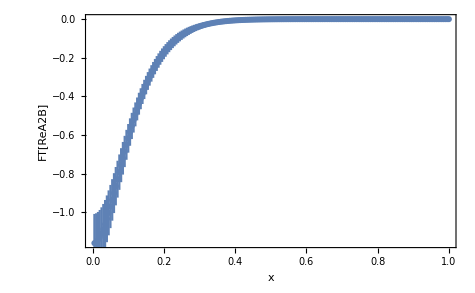
Gaussian-type fit for Re  for =-3
3 are SELECTED for fit!
210 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(c+d) b_L^2+d b_T^2)^-j | a c
d j | ⟨0.194(44)⟩_(2902J) ⟨0.021(20)⟩_(2902J)
⟨0.021(20)⟩_(2902J) ⟨2.1(13)⟩_(2902J) | 0.779431 | 327.567 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-3,2,10]
```

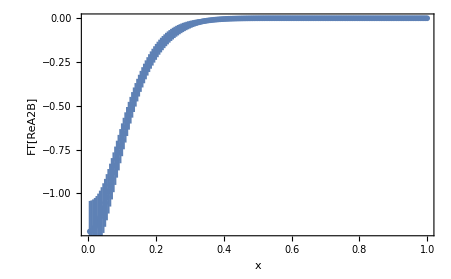
Gaussian-type fit for Re  for =-3
3 are SELECTED for fit!
310 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(c+d) b_L^2+d b_T^2)^-j | a c
d j | ⟨0.202(52)⟩_(2902J) ⟨0.012(18)⟩_(2902J)
⟨0.012(18)⟩_(2902J) ⟨1.3(31)⟩_(2902J) | 0.75776 | 283.825 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-3,3,10]
```

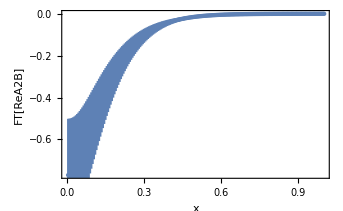
Gaussian-type fit for Re  for =-3
2 are SELECTED for fit!
510 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a ⅇ^(-f η) (1+(c+d) b_L^2+d b_T^2)^-j | a c
d f
j | ⟨0.45(24)⟩_(2902J)  ⟨0.083(75)⟩_(2902J)
⟨0.083(75)⟩_(2902J) ⟨0.404(54)⟩_(2902J)
⟨2.00(78)⟩_(2902J) | 0.942477 | 344.579 | -Graphics-

```mathematica
FitetarangeListReA2B[2,-3,5,10]
```

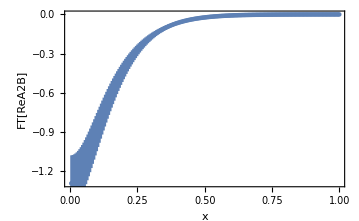
Gaussian-type fit for Re  for =-3
2 are SELECTED for fit!
510 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(c+d) b_L^2+d b_T^2)^-j | a c
d j | ⟨0.76(26)⟩_(2902J)  ⟨0.082(72)⟩_(2902J)
⟨0.082(72)⟩_(2902J) ⟨2.03(76)⟩_(2902J) | 0.98839 | 359.867 | -Graphics-

```mathematica
FitetarangeListReA2B[2,-3,5,10]
```

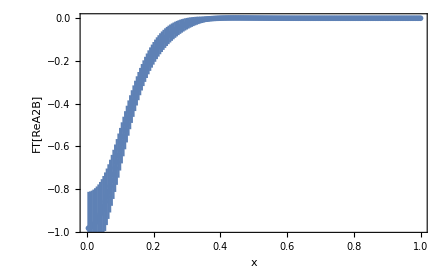
Gaussian-type fit for Re  for =-3
3 are SELECTED for fit!
410 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(c+d) b_L^2+d b_T^2)^-j | a c
d j | ⟨0.160(52)⟩_(2902J)     ⟨0.001 ± 0.018⟩_(2902J)
⟨0.001 ± 0.018⟩_(2902J) ⟨-70(28)⟩_(2902J) | 0.735647 | 241.936 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-3,4,10]
```

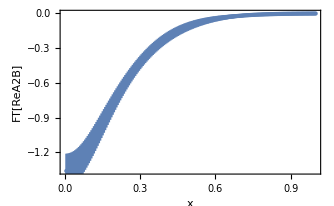
Gaussian-type fit for Re  for =-2
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  k1
k2 j | ⟨0.66(41)⟩_(2902J)  ⟨0.028(56)⟩_(2902J)
⟨0.028(56)⟩_(2902J) ⟨3. ± 18.⟩_(2902J)
⟨-1.1(74)⟩_(2902J)  ⟨2.2(14)⟩_(2902J) | 0.923569 | 218.879 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-2,6,10]
```

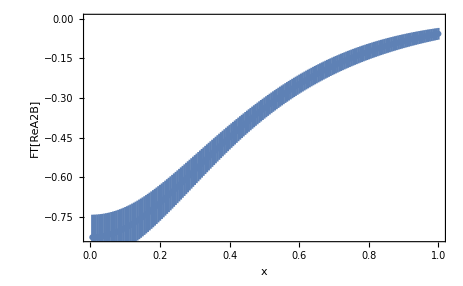
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  k1
k2 j | ⟨0.77(40)⟩_(2902J)  ⟨0.028(44)⟩_(2902J)
⟨0.029(44)⟩_(2902J) ⟨-3. ± 15.⟩_(2902J)
⟨-3.5(64)⟩_(2902J)  ⟨2.3(16)⟩_(2902J) | 0.603916 | 147.277 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

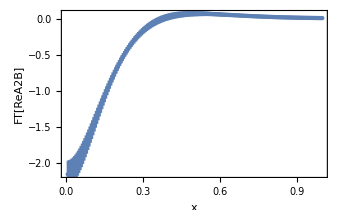
Gaussian-type fit for Re  for =-2
3 are SELECTED for fit!
510 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(d+c (1-k1/η)) b_L^2+d b_T^2)^-j | a c
d k1
j | ⟨0.79(25)⟩_(2902J)  ⟨-0.022(45)⟩_(2902J)
⟨0.056(40)⟩_(2902J) ⟨4.61(84)⟩_(2902J)
⟨2.22(86)⟩_(2902J) | 1.04277 | 292.59 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-2,5,10]
```

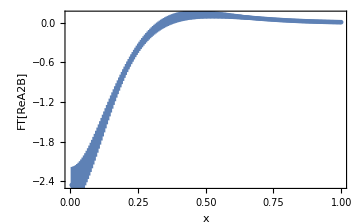
Gaussian-type fit for Re  for =-2
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(d+c (1-k1/η)) b_L^2+d b_T^2)^-j | a c
d k1
j | ⟨0.75(40)⟩_(2902J)  ⟨-0.060(63)⟩_(2902J)
⟨0.037(55)⟩_(2902J) ⟨3.0(17)⟩_(2902J)
⟨2.1(14)⟩_(2902J) | 0.980837 | 230.688 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-2,6,10]
```

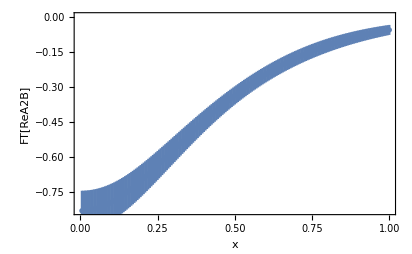
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a (1+(d+c (1-k1/η)) b_L^2+d b_T^2)^-j | a c
d k1
j | ⟨0.78(37)⟩_(2902J)  ⟨0.030(42)⟩_(2902J)
⟨0.030(42)⟩_(2902J) ⟨5.4(15)⟩_(2902J)
⟨2.2(16)⟩_(2902J) | 0.631877 | 152.172 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

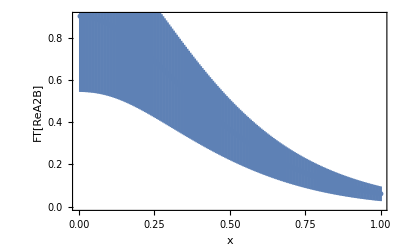
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
-a ⅇ^(-f η) (1+(d+c (1-k1/η)) b_L^2+d b_T^2)^-j | a  c
d  f
k1 j | ⟨0.83(59)⟩_(2902J)  ⟨0.030(42)⟩_(2902J)
⟨0.030(42)⟩_(2902J) ⟨0.517(59)⟩_(2902J)
⟨5.3(16)⟩_(2902J)   ⟨2.2(16)⟩_(2902J) | 0.611115 | 148.89 | -Graphics-

```mathematica
FitetarangeListReA2B[3,-1,6,10]
```

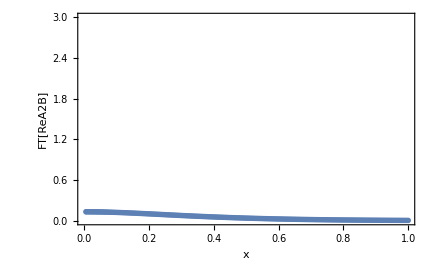
Gaussian-type fit for Re  for =-4
1 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  f
k1 k2
j | ⟨2.12(34)⟩_(2902J)  ⟨2.50(96)⟩_(2902J)
⟨0.46(15)⟩_(2902J)  ⟨0.1767(73)⟩_(2902J)
⟨-5.28(38)⟩_(2902J) ⟨-4.81(13)⟩_(2902J)
⟨2.28(34)⟩_(2902J) | 1.52698 | 499.579 | -Graphics-

```mathematica
FitetarangeListReA2B[1,-4,6,10]
```

```mathematica
GiveParaFitA12BA2B[P1_,etamin_, etamax_, bminForFit_]:=Module[{dataforfitA2B,modelfitA2Bwithf, modelfitA2B,fitJKA2Bwithf, fitJKA2B, fitParasReA2B, fitParasA2Bwithf,fA2B, results, dataforfitImA2B, modelfitImA2B, fitJKImA2B, fitParasImA2B, dataforfitA12B, modelfitA12B, fitJKA12B, fitParasA12B},
results={};
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
Print[etamin,"",etamax," are SELECTED for fit!"];

modelfitA2Bwithf[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2Bwithf=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2Bwithf[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-5.81},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitA2Bwithf];
fitParasA2Bwithf=FitParameters/. fitJKA2Bwithf;
AppendTo[results,{" (with f)",modelfitA2Bwithf[,,,{a,c, d,f,k1,k2,j}],"{a,c,d,f,k1,k2,j}",OutputForm[fitParasA2Bwithf],OutputForm[chisquareDoF/. fitJKA2Bwithf]}];
Print[TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];
fA2B=meanfromJK[fitParasA2Bwithf[[4]]];
Print["Fix f = ",fA2B,"; All data is divided by  "];
results={};

dataforfitA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitA2B ;
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_}]:=a/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{k1,-5.81},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitA2B];
fitParasReA2B=FitParameters/. fitJKA2B;
AppendTo[results,{"",modelfitA2B[,,,{a,c, d,k1,k2,j}],"{a,c,d,k1,k2,j}",OutputForm[fitParasReA2B],OutputForm[chisquareDoF/. fitJKA2B]}];

dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitImA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitImA2B ;
modelfitImA2B[x1_,x2_,x3_,{a_,c_,d_}]:=a*x2/(1+c*x2^2+d*(x2^2+x3^2))^2;
fitJKImA2B=JackknifeFit4DGaussianCons[dataforfitImA2B,modelfitImA2B[n,bL,bT,{a,c,d}],{{a,0.211},{c,0.045},{d,0.045}},{n,bL,bT},modelfitImA2B];
fitParasImA2B=FitParameters/.fitJKImA2B;
AppendTo[results,{"",modelfitImA2B[,,,{a,c, d}],"{a,c,d}",OutputForm[fitParasImA2B],OutputForm[chisquareDoF/.fitJKImA2B]}];


dataforfitA12B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=(etamin)&&#[[1]]<=(etamax)&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(*Print[etamin-1,"",etamax," are SELECTED for fit!"];
Print["2"," are SELECTED for only A12B fit!"];*)
dataforfitA12B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitA12B ;
modelfitA12B[x1_,x2_,x3_,{a_,c_,d_,j_}]:=-(a)/(1+(d+c)*x2^2+d*x3^2)^j;
fitJKA12B=JackknifeFit4DGaussianCons[dataforfitA12B,modelfitA12B[n,bL,bT,{a,c,d,nparam}],{{a,1.02},{c,0.08},{d,0.005},{nparam,2.3}},{n,bL,bT},modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
AppendTo[results,{"",modelfitA12B[,,,{a,c, d, j}],"{a,c,d,j}",OutputForm[fitParasA12B],OutputForm[chisquareDoF/.fitJKA12B]}];

Print[TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];
Return[{fitParasReA2B, fitParasImA2B,fitParasA12B}]
];

PrintxA2B[ParaFitReA2BImA2BA12B_, P1_, b2_]:=Module[{fourieA2Bxforplot, fourieReA2Bxforplot, fourieImA2Bxforplot, fourierREA2Bforx, ParaFitReA2B, ParaFitImA2B, ParaFitA12B, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, aImA2B, cImA2B, dImA2B, fourierIMA2Bforx, fourierA2Bforx, aA12B, cA12B, dA12B, jA12B, fourierReA2B, fourierImA2B,fourierA12Bforx,  PlotfourieReA2Bx, PlotfourieImA2Bx, PlotfourieA2Bx,fourieA12Bxforplot,PlotfourieA12Bx,massterm,MassN,siversx,siversforx,PlotSiversx,xtimessiversx,PlotxtimesSiversx,mxf1T,fourierA12B,Plotmxf1Tx,IntList ={},IntReA2Binfinf, IntReA2B01,IntReA2Bm1p1, IntImA2Binfinf, IntImA2B01, IntImA2Bm1p1, IntReA12Binfinf,IntReA12B01,IntReA12Bm1p1},
Print[" Infinity"];
Print["=",b2];
ParaFitReA2B=ParaFitReA2BImA2BA12B[[1]];
ParaFitImA2B=ParaFitReA2BImA2BA12B[[2]];
ParaFitA12B=ParaFitReA2BImA2BA12B[[3]];
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = ParaFitReA2B[[1]] ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[6]];

aImA2B = (ParaFitImA2B[[1]])/(P1) ;
dImA2B=II+ParaFitImA2B[[3]]*b2;
cImA2B = (ParaFitImA2B[[2]])/(P1^2) ;

aA12B = -(ParaFitA12B[[1]]) ;
cA12B = (ParaFitA12B[[2]])/(P1^2) ;
dA12B = II+ParaFitA12B[[3]] *b2;
jA12B = ParaFitA12B[[4]];

fourierReA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];
fourierImA2B[x_, {a_,d_,c_}] :=( a E^(-((Sqrt[d] x)/Sqrt[c])) Sqrt[π/2] x ((-1+E^((2 Sqrt[d] x)/Sqrt[c])) Sign[x] (-1+Sign[Abs[Re[Sqrt[d]/Sqrt[c]]]])+2 (E^((2 Sqrt[d] x)/Sqrt[c]) HeavisideTheta[-x Sign[Re[Sqrt[d]/Sqrt[c]]]]+HeavisideTheta[x Sign[Re[Sqrt[d]/Sqrt[c]]]]) Sign[Re[Sqrt[d]/Sqrt[c]]]))/(4 c^(3/2) Sqrt[d]);
fourierA12B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];

MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-1,etav->8, bNum->even}],MN][[1]];
massterm=MassN*(197*0.001/lata);

IntReA2Binfinf = NFourierTransformJK[fourierReA2B, {aReA2B, dReA2B, cReA2B, jReA2B}, -Infinity,Infinity];
IntReA2B01= NFourierTransformJK[fourierReA2B, {aReA2B, dReA2B, cReA2B, jReA2B}, 0,1];
IntReA2Bm1p1 = NFourierTransformJK[fourierReA2B, {aReA2B, dReA2B, cReA2B, jReA2B}, -1,1];

IntImA2Binfinf = NFourierTransformJK[fourierImA2B, {aImA2B, dImA2B, cImA2B}, -Infinity,Infinity];
IntImA2B01= NFourierTransformJK[fourierImA2B, {aImA2B, dImA2B, cImA2B}, 0,1];
IntImA2Bm1p1 = NFourierTransformJK[fourierImA2B, {aImA2B, dImA2B, cImA2B}, -1,1];

IntReA12Binfinf = NFourierTransformJK[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, -Infinity,Infinity];
IntReA12B01= NFourierTransformJK[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, 0,1];
IntReA12Bm1p1 = NFourierTransformJK[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, -1,1];

AppendTo[IntList ,{"  ",OutputForm[IntReA2Binfinf],OutputForm[IntReA2Bm1p1],OutputForm[IntReA2B01]}];
AppendTo[IntList ,{"i  ",OutputForm[IntImA2Binfinf],OutputForm[IntImA2Bm1p1],OutputForm[IntImA2B01]}];
AppendTo[IntList ,{"= = 2  ",OutputForm[2*(IntReA2Binfinf-IntImA2Binfinf)],OutputForm[2*(IntReA2Bm1p1-IntImA2Bm1p1)],OutputForm[2*(IntReA2B01-IntImA2B01)]}];
AppendTo[IntList ,{"= = -2  ",OutputForm[-2*IntReA12Binfinf],OutputForm[-2*IntReA12Bm1p1],OutputForm[-2*IntReA12B01]}];
AppendTo[IntList ,{"",OutputForm[-massterm*IntReA12Binfinf/(IntReA2Binfinf-IntImA2Binfinf)],OutputForm[-massterm*IntReA12Bm1p1/(IntReA2Bm1p1-IntImA2Bm1p1)],OutputForm[-massterm*IntReA12B01/(IntReA2B01-IntImA2B01)]}];
Print[TableForm[IntList,TableHeadings->{None,{"{a,b}->","{-Infinity, Infinity}","{-1, +1}","{0, +1}"}},TableSpacing->{1,2}]];


fourieReA2Bxforplot={};
fourieImA2Bxforplot={};
fourieA2Bxforplot={};
mxf1T={};
fourieA12Bxforplot={};
siversx={};
xtimessiversx={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierReA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
fourierIMA2Bforx=modelfitJackkifex3para[fourierImA2B,{aImA2B,dImA2B,cImA2B}, x];
fourierA2Bforx=2*(fourierREA2Bforx-fourierIMA2Bforx);
fourierA12Bforx=-2*(modelfitJackkifex[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, x]);
siversforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
AppendTo[fourieImA2Bxforplot,{x,fourierIMA2Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[mxf1T,{x,massterm*x*fourierA12Bforx}];
AppendTo[siversx,{x,siversforx}];
AppendTo[xtimessiversx,{x,x*siversforx}];
,{x,0,1, 0.005}];
Print[  ""];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , ""}, Frame->True , PlotRange->Full];
Print[PlotfourieReA2Bx];
Print["i"];
PlotfourieImA2Bx= ErrorListPlot[MakeErrBars[fourieImA2Bxforplot],FrameLabel->{ , "i"}, Frame->True , PlotRange->Full];
Print[PlotfourieImA2Bx];
Print[" =  + i(i)"];
Print["=  =  - "];
PlotfourieA2Bx= ErrorListPlot[MakeErrBars[fourieA2Bxforplot],FrameLabel->{ , ""}, Frame->True , PlotRange->Full];
Print[PlotfourieA2Bx];
Print[  " =  "];
PlotfourieA12Bx= ErrorListPlot[MakeErrBars[fourieA12Bxforplot],FrameLabel->{ , ""}, Frame->True , PlotRange->Full];
Print[PlotfourieA12Bx];
Plotmxf1Tx= ErrorListPlot[MakeErrBars[mxf1T],FrameLabel->{ , "(GeV)"}, Frame->True , PlotRange->Full];
Print[Plotmxf1Tx];
Print["= "];
PlotSiversx= ErrorListPlot[MakeErrBars[siversx],FrameLabel->{ , "(GeV)"}, Frame->True , PlotRange->Full];
Print[PlotSiversx];
PlotxtimesSiversx= ErrorListPlot[MakeErrBars[xtimessiversx],FrameLabel->{ , "(GeV)"}, Frame->True , PlotRange->Full];
Print[PlotxtimesSiversx];
];
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨4.01(58)⟩_(2902J), ⟨0.43(17)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.496(12)⟩_(2902J), ⟨-5.81(33)⟩_(2902J), ⟨-4.86(14)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.56911

Fix f = 0.495923; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨4.03(40)⟩_(2902J), ⟨0.43(17)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨-5.83(30)⟩_(2902J), ⟨-4.86(12)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.62298
 | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.153(31)⟩_(2902J), ⟨0.0345(56)⟩_(2902J), ⟨0.0345(56)⟩_(2902J)} | 1.47336
 | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.59(25)⟩_(2902J), ⟨0.019(37)⟩_(2902J), ⟨0.019(37)⟩_(2902J), ⟨1.9(18)⟩_(2902J)} | 0.890361

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
   | ⟨2.832(41)⟩_(2902J) | ⟨2.05(21)⟩_(2902J) | ⟨1.03(11)⟩_(2902J)
i   |               -15
⟨30.2(26) × 10   ⟩_(2902J) |               -15
⟨24.3(23) × 10   ⟩_(2902J) | ⟨-0.342(27)⟩_(2902J)
= = 2   | ⟨5.665(82)⟩_(2902J) | ⟨4.11(41)⟩_(2902J) | ⟨2.74(21)⟩_(2902J)
= = -2   | ⟨1.55(19)⟩_(2902J) | ⟨1.52(17)⟩_(2902J) | ⟨0.761(85)⟩_(2902J)
 | ⟨0.294(36)⟩_(2902J) | ⟨0.395(60)⟩_(2902J) | ⟨0.297(41)⟩_(2902J)

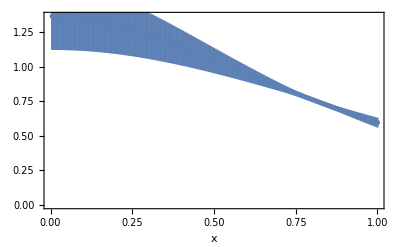

i

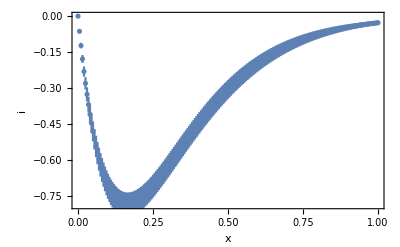

=  + i(i)

=  =  -

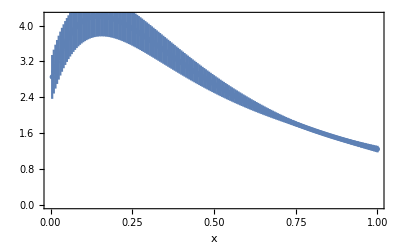

=

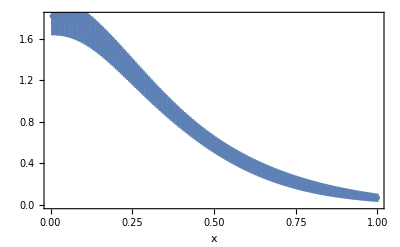

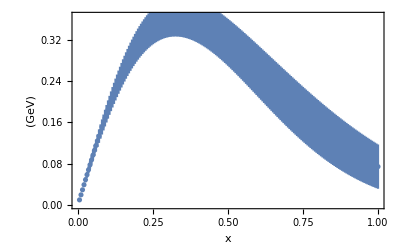

=

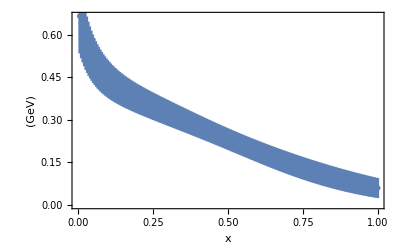

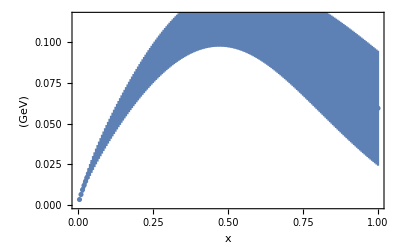

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,6, 10, 3];
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨2.42(38)⟩_(2902J), ⟨0.201(89)⟩_(2902J), ⟨0.040(11)⟩_(2902J), ⟨0.511(17)⟩_(2902J), ⟨-5.06(29)⟩_(2902J), ⟨-4.53(13)⟩_(2902J), ⟨3.10(46)⟩_(2902J)} | 1.36736

Fix f = 0.51122; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨2.44(22)⟩_(2902J), ⟨0.199(89)⟩_(2902J), ⟨0.040(11)⟩_(2902J), ⟨-5.08(25)⟩_(2902J), ⟨-4.54(11)⟩_(2902J), ⟨3.11(45)⟩_(2902J)} | 1.39846
 | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.215(29)⟩_(2902J), ⟨0.0306(33)⟩_(2902J), ⟨0.0306(33)⟩_(2902J)} | 2.33676
 | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.51(17)⟩_(2902J), ⟨0.040(41)⟩_(2902J), ⟨0.040(41)⟩_(2902J), ⟨1.97(76)⟩_(2902J)} | 1.36334

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
   | ⟨2.260(44)⟩_(2902J) | ⟨2.161(89)⟩_(2902J) | ⟨1.080(45)⟩_(2902J)
i   |                 -15
⟨-596.5(90) × 10   ⟩_(2902J) |                -15
⟨225.5(41) × 10   ⟩_(2902J) | ⟨-0.537(34)⟩_(2902J)
= = 2   | ⟨4.520(88)⟩_(2902J) | ⟨4.32(18)⟩_(2902J) | ⟨3.24(12)⟩_(2902J)
= = -2   | ⟨1.17(11)⟩_(2902J) | ⟨1.17(11)⟩_(2902J) | ⟨0.584(54)⟩_(2902J)
 | ⟨0.278(26)⟩_(2902J) | ⟨0.290(30)⟩_(2902J) | ⟨0.194(20)⟩_(2902J)

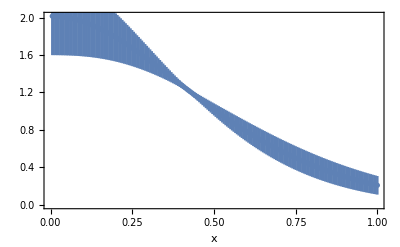

i

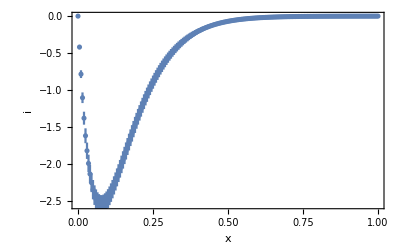

=  + i(i)

=  =  -

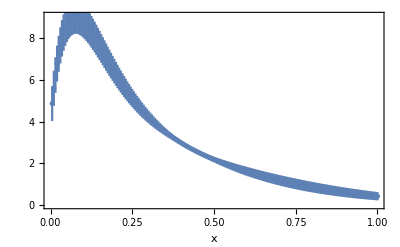

=

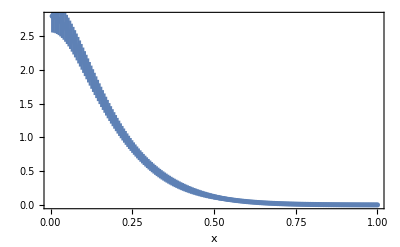

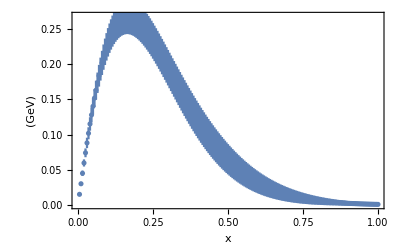

=

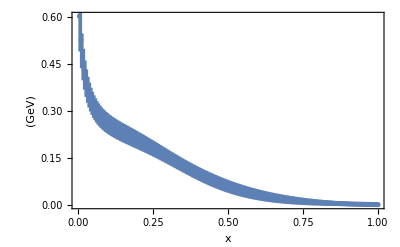

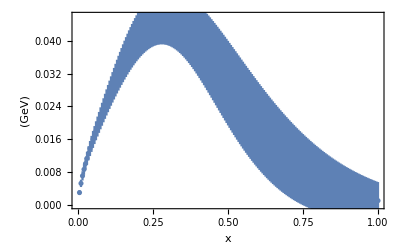

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,5, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

2.8 are SELECTED for fit!

410 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.63(23)⟩_(2902J), ⟨0.134(64)⟩_(2902J), ⟨0.032(14)⟩_(2902J), ⟨0.451(16)⟩_(2902J), ⟨-3.80(51)⟩_(2902J), ⟨-3.93(24)⟩_(2902J), ⟨3.8(12)⟩_(2902J)} | 1.66245

Fix f = 0.451384; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.64(14)⟩_(2902J), ⟨0.130(69)⟩_(2902J), ⟨0.032(13)⟩_(2902J), ⟨-3.81(51)⟩_(2902J), ⟨-3.94(24)⟩_(2902J), ⟨3.8(11)⟩_(2902J)} | 1.68166
 | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.208(28)⟩_(2902J), ⟨0.0373(39)⟩_(2902J), ⟨0.0373(39)⟩_(2902J)} | 1.57915
 | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.223(70)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨1.6(28)⟩_(2902J)} | 0.885999

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
   | ⟨1.414(46)⟩_(2902J) | ⟨1.412(47)⟩_(2902J) | ⟨0.706(24)⟩_(2902J)
i   |                 -15
⟨-140.5(69) × 10   ⟩_(2902J) |               -15
⟨78.6(27) × 10   ⟩_(2902J) | ⟨-0.438(34)⟩_(2902J)
= = 2   | ⟨2.828(91)⟩_(2902J) | ⟨2.825(93)⟩_(2902J) | ⟨2.288(82)⟩_(2902J)
= = -2   | ⟨0.569(88)⟩_(2902J) | ⟨0.569(88)⟩_(2902J) | ⟨0.284(44)⟩_(2902J)
 | ⟨0.216(34)⟩_(2902J) | ⟨0.217(34)⟩_(2902J) | ⟨0.134(22)⟩_(2902J)

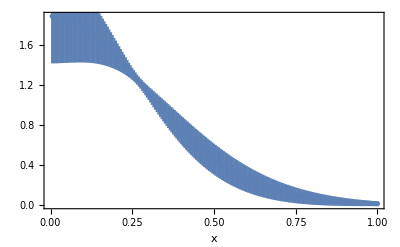

i

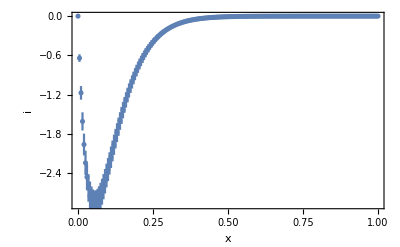

=  + i(i)

=  =  -

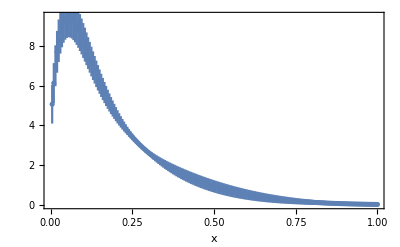

=

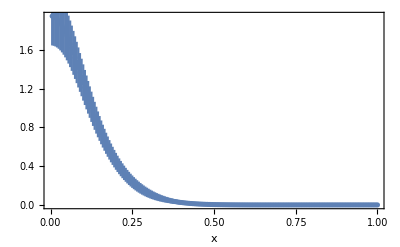

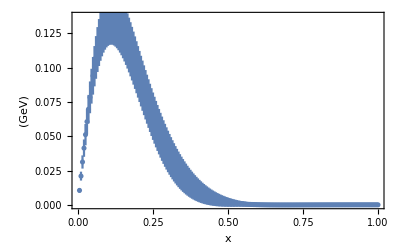

=

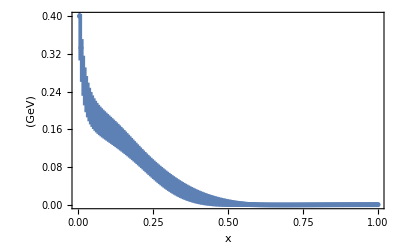

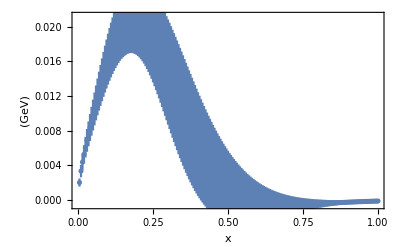

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,4, 10, 2.8];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

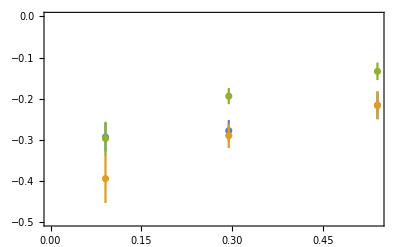

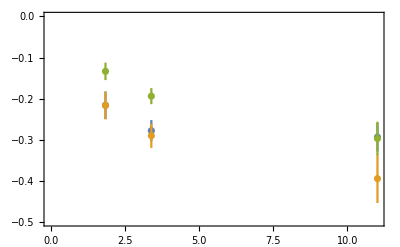

```mathematica
i1 = "⟨0.294(36)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i2="⟨0.278(26)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i3="⟨0.216(34)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";

i1m1p1 = "⟨0.395(60)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i2m1p1="⟨0.290(30)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i3m1p1="⟨0.217(34)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";

i10p1 = "⟨0.297(41)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i20p1="⟨0.194(20)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i30p1="⟨0.134(22)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";

zetaxintegral ={{0.09077,-i1}, {0.2944,-i2},{0.540, -i3}};
zetaxintegralm1p1 ={{0.09077,-i1m1p1}, {0.2944,-i2m1p1},{0.540, -i3m1p1}};
zetaxintegral0p1 ={{0.09077,-i10p1}, {0.2944,-i20p1},{0.540, -i30p1}};
ErrorListPlot[{MakeErrBars[zetaxintegral],MakeErrBars[zetaxintegralm1p1],MakeErrBars[zetaxintegral0p1]},FrameLabel->{"", ""},PlotLegends->{"","",""}, Frame->True , PlotRange->{{0,Automatic},{0,-0.5}}]
zetaxintegral ={{1/0.09077,-i1}, {1/0.2944,-i2},{1/0.540, -i3}};
zetaxintegralm1p1 ={{1/0.09077,-i1m1p1}, {1/0.2944,-i2m1p1},{1/0.540, -i3m1p1}};
zetaxintegral0p1 ={{1/0.09077,-i10p1}, {1/0.2944,-i20p1},{1/0.540, -i30p1}};
ErrorListPlot[{MakeErrBars[zetaxintegral],MakeErrBars[zetaxintegralm1p1],MakeErrBars[zetaxintegral0p1]},FrameLabel->{"", ""},PlotLegends->{"","",""}, Frame->True , PlotRange->{{0,Automatic},{0,-0.5}}]
```

```mathematica
GiveParaFitA12BA2B[P1_,etamin_, etamax_, bminForFit_]:=Module[{dataforfitA2B,modelfitA2Bwithf, modelfitA2B,fitJKA2Bwithf, fitJKA2B, fitParasReA2B, fitParasA2Bwithf,fA2B, results, dataforfitImA2B, modelfitImA2B, fitJKImA2B, fitParasImA2B, dataforfitA12B, modelfitA12B, fitJKA12B, fitParasA12B},
results={};
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
Print[etamin,"",etamax," are SELECTED for fit!"];

modelfitA2Bwithf[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1-k2*Log[x1]/x1))*x2^2+d*x3^2)^j;
fitJKA2Bwithf=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2Bwithf[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-4.50},{k2,5.94},{nparam,2.06}},{n,bL,bT},modelfitA2Bwithf];
fitParasA2Bwithf=FitParameters/. fitJKA2Bwithf;
AppendTo[results,{" (with f)",modelfitA2Bwithf[,,,{a,c, d,f,k1,k2,j}],"{a,c,d,f,k1,k2,j}",OutputForm[fitParasA2Bwithf],OutputForm[chisquareDoF/. fitJKA2Bwithf]}];
Print[TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];
fA2B=meanfromJK[fitParasA2Bwithf[[4]]];
Print["Fix f = ",fA2B,"; All data is divided by  "];
results={};

dataforfitA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitA2B ;
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_}]:=a/(1+(d+c*(1-k1/x1-k2*Log[x1]/x1))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{k1,-4.50},{k2,5.94},{nparam,2.06}},{n,bL,bT},modelfitA2B];
fitParasReA2B=FitParameters/. fitJKA2B;
AppendTo[results,{"",modelfitA2B[,,,{a,c, d,k1,k2,j}],"{a,c,d,k1,k2,j}",OutputForm[fitParasReA2B],OutputForm[chisquareDoF/. fitJKA2B]}];

dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitImA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitImA2B ;
modelfitImA2B[x1_,x2_,x3_,{a_,c_,d_}]:=a*x2/(1+c*x2^2+d*(x2^2+x3^2))^2;
fitJKImA2B=JackknifeFit4DGaussianCons[dataforfitImA2B,modelfitImA2B[n,bL,bT,{a,c,d}],{{a,0.211},{c,0.045},{d,0.045}},{n,bL,bT},modelfitImA2B];
fitParasImA2B=FitParameters/.fitJKImA2B;
AppendTo[results,{"",modelfitImA2B[,,,{a,c, d}],"{a,c,d}",OutputForm[fitParasImA2B],OutputForm[chisquareDoF/.fitJKImA2B]}];


dataforfitA12B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=(etamin)&&#[[1]]<=(etamax)&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(*Print[etamin-1,"",etamax," are SELECTED for fit!"];
Print["2"," are SELECTED for only A12B fit!"];*)
dataforfitA12B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitA12B ;
modelfitA12B[x1_,x2_,x3_,{a_,c_,d_,j_}]:=-(a)/(1+(d+c)*x2^2+d*x3^2)^j;
fitJKA12B=JackknifeFit4DGaussianCons[dataforfitA12B,modelfitA12B[n,bL,bT,{a,c,d,nparam}],{{a,1.02},{c,0.08},{d,0.005},{nparam,2.3}},{n,bL,bT},modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
AppendTo[results,{"",modelfitA12B[,,,{a,c, d, j}],"{a,c,d,j}",OutputForm[fitParasA12B],OutputForm[chisquareDoF/.fitJKA12B]}];

Print[TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];
Return[{fitParasReA2B, fitParasImA2B,fitParasA12B}]
];

PrintxA2B[ParaFitReA2BImA2BA12B_, P1_, b2_]:=Module[{fourieA2Bxforplot, fourieReA2Bxforplot, fourieImA2Bxforplot, fourierREA2Bforx, ParaFitReA2B, ParaFitImA2B, ParaFitA12B, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, aImA2B, cImA2B, dImA2B, fourierIMA2Bforx, fourierA2Bforx, aA12B, cA12B, dA12B, jA12B, fourierReA2B, fourierImA2B,fourierA12Bforx,  PlotfourieReA2Bx, PlotfourieImA2Bx, PlotfourieA2Bx,fourieA12Bxforplot,PlotfourieA12Bx,massterm,MassN,siversx,siversforx,PlotSiversx,xtimessiversx,PlotxtimesSiversx,mxf1T,fourierA12B,Plotmxf1Tx,IntList ={},IntReA2Binfinf, IntReA2B01,IntReA2Bm1p1, IntImA2Binfinf, IntImA2B01, IntImA2Bm1p1, IntReA12Binfinf,IntReA12B01,IntReA12Bm1p1},
Print[" Infinity"];
Print["=",b2];
ParaFitReA2B=ParaFitReA2BImA2BA12B[[1]];
ParaFitImA2B=ParaFitReA2BImA2BA12B[[2]];
ParaFitA12B=ParaFitReA2BImA2BA12B[[3]];
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = ParaFitReA2B[[1]] ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[6]];

aImA2B = (ParaFitImA2B[[1]])/(P1) ;
dImA2B=II+ParaFitImA2B[[3]]*b2;
cImA2B = (ParaFitImA2B[[2]])/(P1^2) ;

aA12B = -(ParaFitA12B[[1]]) ;
cA12B = (ParaFitA12B[[2]])/(P1^2) ;
dA12B = II+ParaFitA12B[[3]] *b2;
jA12B = ParaFitA12B[[4]];

fourierReA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];
fourierImA2B[x_, {a_,d_,c_}] :=( a E^(-((Sqrt[d] x)/Sqrt[c])) Sqrt[π/2] x ((-1+E^((2 Sqrt[d] x)/Sqrt[c])) Sign[x] (-1+Sign[Abs[Re[Sqrt[d]/Sqrt[c]]]])+2 (E^((2 Sqrt[d] x)/Sqrt[c]) HeavisideTheta[-x Sign[Re[Sqrt[d]/Sqrt[c]]]]+HeavisideTheta[x Sign[Re[Sqrt[d]/Sqrt[c]]]]) Sign[Re[Sqrt[d]/Sqrt[c]]]))/(4 c^(3/2) Sqrt[d]);
fourierA12B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];

MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-1,etav->8, bNum->even}],MN][[1]];
massterm=MassN*(197*0.001/lata);

IntReA2Binfinf = NFourierTransformJK[fourierReA2B, {aReA2B, dReA2B, cReA2B, jReA2B}, -Infinity,Infinity];
IntReA2B01= NFourierTransformJK[fourierReA2B, {aReA2B, dReA2B, cReA2B, jReA2B}, 0,1];
IntReA2Bm1p1 = NFourierTransformJK[fourierReA2B, {aReA2B, dReA2B, cReA2B, jReA2B}, -1,1];

IntImA2Binfinf = NFourierTransformJK[fourierImA2B, {aImA2B, dImA2B, cImA2B}, -Infinity,Infinity];
IntImA2B01= NFourierTransformJK[fourierImA2B, {aImA2B, dImA2B, cImA2B}, 0,1];
IntImA2Bm1p1 = NFourierTransformJK[fourierImA2B, {aImA2B, dImA2B, cImA2B}, -1,1];

IntReA12Binfinf = NFourierTransformJK[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, -Infinity,Infinity];
IntReA12B01= NFourierTransformJK[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, 0,1];
IntReA12Bm1p1 = NFourierTransformJK[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, -1,1];

AppendTo[IntList ,{"  ",OutputForm[IntReA2Binfinf],OutputForm[IntReA2Bm1p1],OutputForm[IntReA2B01]}];
AppendTo[IntList ,{"i  ",OutputForm[IntImA2Binfinf],OutputForm[IntImA2Bm1p1],OutputForm[IntImA2B01]}];
AppendTo[IntList ,{"= = 2  ",OutputForm[2*(IntReA2Binfinf-IntImA2Binfinf)],OutputForm[2*(IntReA2Bm1p1-IntImA2Bm1p1)],OutputForm[2*(IntReA2B01-IntImA2B01)]}];
AppendTo[IntList ,{"= = -2  ",OutputForm[-2*IntReA12Binfinf],OutputForm[-2*IntReA12Bm1p1],OutputForm[-2*IntReA12B01]}];
AppendTo[IntList ,{"",OutputForm[-massterm*IntReA12Binfinf/(IntReA2Binfinf-IntImA2Binfinf)],OutputForm[-massterm*IntReA12Bm1p1/(IntReA2Bm1p1-IntImA2Bm1p1)],OutputForm[-massterm*IntReA12B01/(IntReA2B01-IntImA2B01)]}];
Print[TableForm[IntList,TableHeadings->{None,{"{a,b}->","{-Infinity, Infinity}","{-1, +1}","{0, +1}"}},TableSpacing->{1,2}]];


fourieReA2Bxforplot={};
fourieImA2Bxforplot={};
fourieA2Bxforplot={};
mxf1T={};
fourieA12Bxforplot={};
siversx={};
xtimessiversx={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierReA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
fourierIMA2Bforx=modelfitJackkifex3para[fourierImA2B,{aImA2B,dImA2B,cImA2B}, x];
fourierA2Bforx=2*(fourierREA2Bforx-fourierIMA2Bforx);
fourierA12Bforx=-2*(modelfitJackkifex[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, x]);
siversforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
AppendTo[fourieImA2Bxforplot,{x,fourierIMA2Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[mxf1T,{x,massterm*x*fourierA12Bforx}];
AppendTo[siversx,{x,siversforx}];
AppendTo[xtimessiversx,{x,x*siversforx}];
,{x,0,1, 0.005}];
Print[  ""];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , ""}, Frame->True , PlotRange->Full];
Print[PlotfourieReA2Bx];
Print["i"];
PlotfourieImA2Bx= ErrorListPlot[MakeErrBars[fourieImA2Bxforplot],FrameLabel->{ , "i"}, Frame->True , PlotRange->Full];
Print[PlotfourieImA2Bx];
Print[" =  + i(i)"];
Print["=  =  - "];
PlotfourieA2Bx= ErrorListPlot[MakeErrBars[fourieA2Bxforplot],FrameLabel->{ , ""}, Frame->True , PlotRange->Full];
Print[PlotfourieA2Bx];
Print[  " =  "];
PlotfourieA12Bx= ErrorListPlot[MakeErrBars[fourieA12Bxforplot],FrameLabel->{ , ""}, Frame->True , PlotRange->Full];
Print[PlotfourieA12Bx];
Plotmxf1Tx= ErrorListPlot[MakeErrBars[mxf1T],FrameLabel->{ , "(GeV)"}, Frame->True , PlotRange->Full];
Print[Plotmxf1Tx];
Print["= "];
PlotSiversx= ErrorListPlot[MakeErrBars[siversx],FrameLabel->{ , "(GeV)"}, Frame->True , PlotRange->Full];
Print[PlotSiversx];
PlotxtimesSiversx= ErrorListPlot[MakeErrBars[xtimessiversx],FrameLabel->{ , "(GeV)"}, Frame->True , PlotRange->Full];
Print[PlotxtimesSiversx];
];
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨4.01(58)⟩_(2902J), ⟨0.240(89)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.496(12)⟩_(2902J), ⟨-4.50(52)⟩_(2902J), ⟨5.94(29)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.56865

Fix f = 0.495914; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 | a (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨4.03(40)⟩_(2902J), ⟨0.239(90)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨-4.52(47)⟩_(2902J), ⟨5.96(26)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.62249
 | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.153(31)⟩_(2902J), ⟨0.0345(56)⟩_(2902J), ⟨0.0345(56)⟩_(2902J)} | 1.47338
 | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.59(25)⟩_(2902J), ⟨0.019(37)⟩_(2902J), ⟨0.019(37)⟩_(2902J), ⟨1.9(18)⟩_(2902J)} | 0.890322

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
   | ⟨2.832(41)⟩_(2902J) | ⟨2.38(16)⟩_(2902J) | ⟨1.189(80)⟩_(2902J)
i   |               -15
⟨12.9(26) × 10   ⟩_(2902J) |                -15
⟨-43.9(23) × 10   ⟩_(2902J) | ⟨-0.342(27)⟩_(2902J)
= = 2   | ⟨5.664(82)⟩_(2902J) | ⟨4.76(32)⟩_(2902J) | ⟨3.06(17)⟩_(2902J)
= = -2   | ⟨1.55(19)⟩_(2902J) | ⟨1.52(17)⟩_(2902J) | ⟨0.761(85)⟩_(2902J)
 | ⟨0.294(36)⟩_(2902J) | ⟨0.342(46)⟩_(2902J) | ⟨0.266(34)⟩_(2902J)

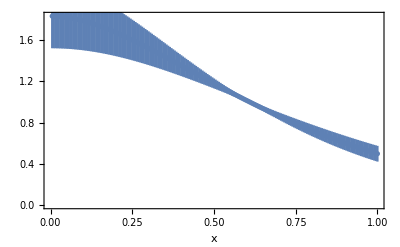

i

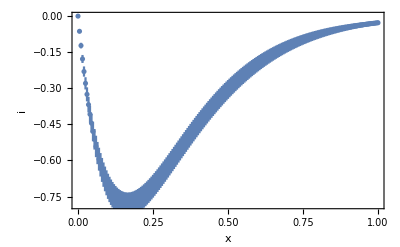

=  + i(i)

=  =  -

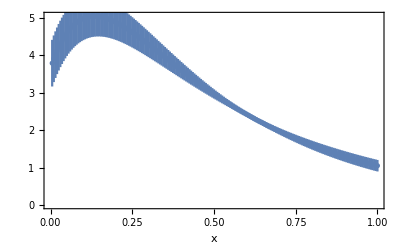

=

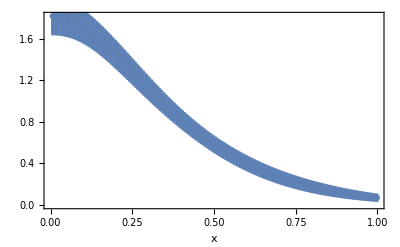

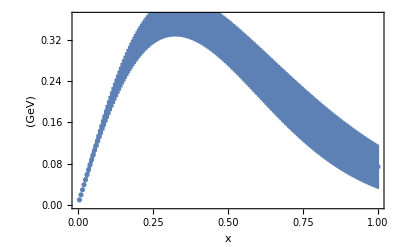

=

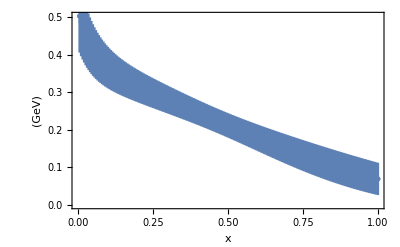

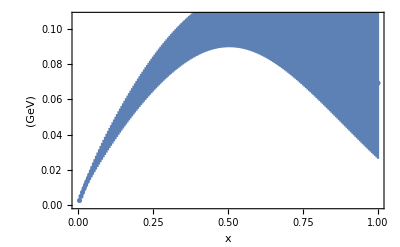

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,6, 10, 3];
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨2.42(38)⟩_(2902J), ⟨0.112(48)⟩_(2902J), ⟨0.040(11)⟩_(2902J), ⟨0.511(17)⟩_(2902J), ⟨-3.18(42)⟩_(2902J), ⟨5.16(26)⟩_(2902J), ⟨3.10(46)⟩_(2902J)} | 1.36778

Fix f = 0.511301; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 | a (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨2.44(22)⟩_(2902J), ⟨0.111(48)⟩_(2902J), ⟨0.040(11)⟩_(2902J), ⟨-3.21(37)⟩_(2902J), ⟨5.19(22)⟩_(2902J), ⟨3.11(45)⟩_(2902J)} | 1.39895
 | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.215(29)⟩_(2902J), ⟨0.0306(33)⟩_(2902J), ⟨0.0306(33)⟩_(2902J)} | 2.33633
 | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.51(17)⟩_(2902J), ⟨0.040(41)⟩_(2902J), ⟨0.040(41)⟩_(2902J), ⟨1.97(76)⟩_(2902J)} | 1.36331

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
   | ⟨2.261(44)⟩_(2902J) | ⟨2.240(52)⟩_(2902J) | ⟨1.120(26)⟩_(2902J)
i   |                 -15
⟨-681.8(88) × 10   ⟩_(2902J) |                 -15
⟨-111.5(41) × 10   ⟩_(2902J) | ⟨-0.538(34)⟩_(2902J)
= = 2   | ⟨4.522(88)⟩_(2902J) | ⟨4.48(11)⟩_(2902J) | ⟨3.315(88)⟩_(2902J)
= = -2   | ⟨1.17(11)⟩_(2902J) | ⟨1.17(11)⟩_(2902J) | ⟨0.584(54)⟩_(2902J)
 | ⟨0.278(26)⟩_(2902J) | ⟨0.281(27)⟩_(2902J) | ⟨0.190(19)⟩_(2902J)

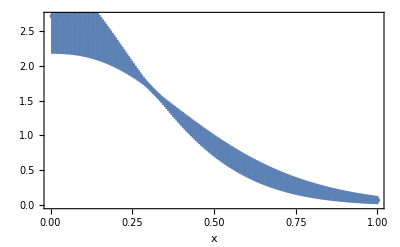

i

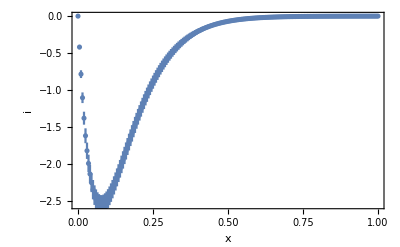

=  + i(i)

=  =  -

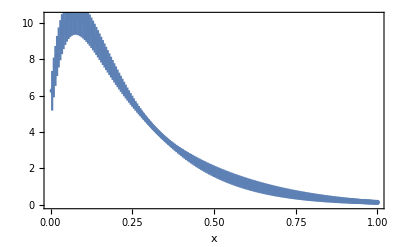

=

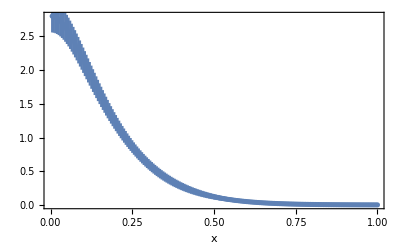

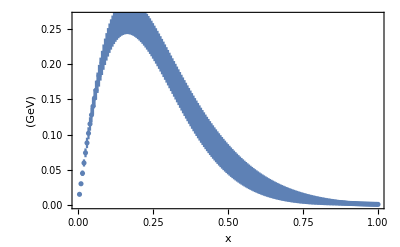

=

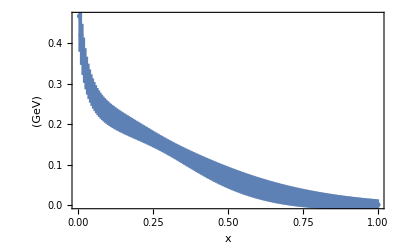

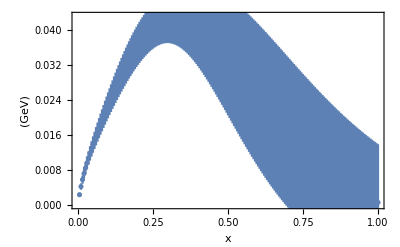

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,5, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

2.8 are SELECTED for fit!

410 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.63(23)⟩_(2902J), ⟨0.079(36)⟩_(2902J), ⟨0.032(14)⟩_(2902J), ⟨0.452(16)⟩_(2902J), ⟨-1.31(60)⟩_(2902J), ⟨3.92(40)⟩_(2902J), ⟨3.8(12)⟩_(2902J)} | 1.66349

Fix f = 0.451545; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
 | a (1+(d+c (1-k1/η-(k2 Log[η])/η)) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.64(14)⟩_(2902J), ⟨0.077(39)⟩_(2902J), ⟨0.032(13)⟩_(2902J), ⟨-1.32(59)⟩_(2902J), ⟨3.93(40)⟩_(2902J), ⟨3.8(11)⟩_(2902J)} | 1.68274
 | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.208(28)⟩_(2902J), ⟨0.0373(39)⟩_(2902J), ⟨0.0373(39)⟩_(2902J)} | 1.57787
 | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.223(70)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨1.6(28)⟩_(2902J)} | 0.885876

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
   | ⟨1.415(46)⟩_(2902J) | ⟨1.415(46)⟩_(2902J) | ⟨0.708(23)⟩_(2902J)
i   |                -15
⟨475.8(68) × 10   ⟩_(2902J) |                -15
⟨222.9(27) × 10   ⟩_(2902J) | ⟨-0.438(34)⟩_(2902J)
= = 2   | ⟨2.831(91)⟩_(2902J) | ⟨2.831(92)⟩_(2902J) | ⟨2.292(80)⟩_(2902J)
= = -2   | ⟨0.569(88)⟩_(2902J) | ⟨0.569(88)⟩_(2902J) | ⟨0.285(44)⟩_(2902J)
 | ⟨0.216(34)⟩_(2902J) | ⟨0.216(34)⟩_(2902J) | ⟨0.133(22)⟩_(2902J)

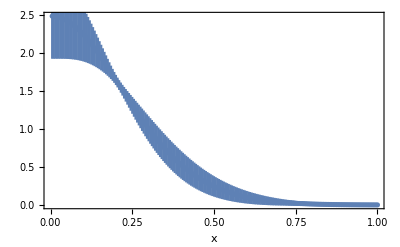

i

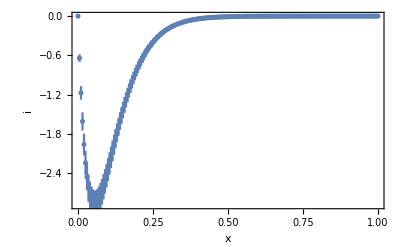

=  + i(i)

=  =  -

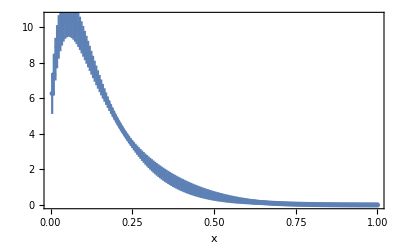

=

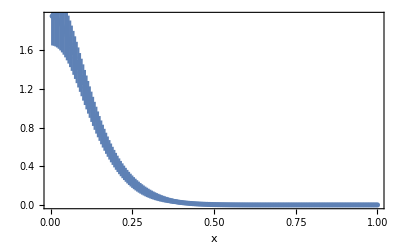

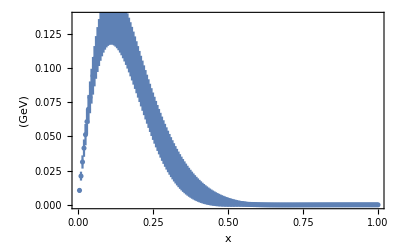

=

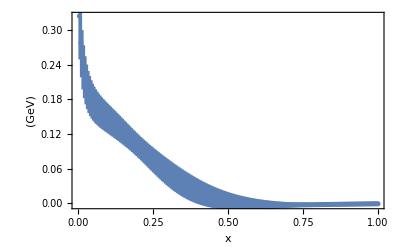

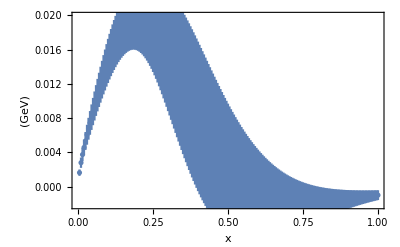

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,4, 10, 2.8];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

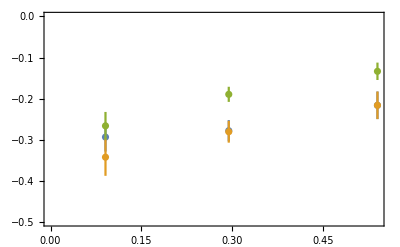

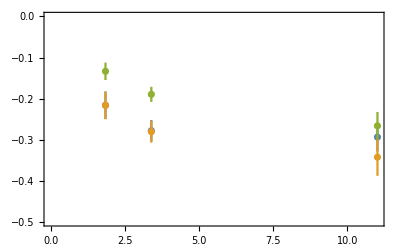

```mathematica
i1 ="⟨0.294(36)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i2="⟨0.278(26)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i3="⟨0.216(34)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";

i1m1p1 = "⟨0.342(46)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i2m1p1="⟨0.281(27)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i3m1p1="⟨0.216(34)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";

i10p1 = "⟨0.266(34)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i20p1="⟨0.190(19)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";
i30p1="⟨0.133(22)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)";

zetaxintegral ={{0.09077,-i1}, {0.2944,-i2},{0.540, -i3}};
zetaxintegralm1p1 ={{0.09077,-i1m1p1}, {0.2944,-i2m1p1},{0.540, -i3m1p1}};
zetaxintegral0p1 ={{0.09077,-i10p1}, {0.2944,-i20p1},{0.540, -i30p1}};
ErrorListPlot[{MakeErrBars[zetaxintegral],MakeErrBars[zetaxintegralm1p1],MakeErrBars[zetaxintegral0p1]},FrameLabel->{"", ""},PlotLegends->{"","",""}, Frame->True , PlotRange->{{0,Automatic},{0,-0.5}}]
zetaxintegral ={{1/0.09077,-i1}, {1/0.2944,-i2},{1/0.540, -i3}};
zetaxintegralm1p1 ={{1/0.09077,-i1m1p1}, {1/0.2944,-i2m1p1},{1/0.540, -i3m1p1}};
zetaxintegral0p1 ={{1/0.09077,-i10p1}, {1/0.2944,-i20p1},{1/0.540, -i30p1}};
ErrorListPlot[{MakeErrBars[zetaxintegral],MakeErrBars[zetaxintegralm1p1],MakeErrBars[zetaxintegral0p1]},FrameLabel->{"", ""},PlotLegends->{"","",""}, Frame->True , PlotRange->{{0,Automatic},{0,-0.5}}]
```

```mathematica
FitetarangeListImA2B[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKA2B,dataforfitA2B,results={}},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*0.4515448970879027]})&/@dataforfitA2B ;

modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_}]:=a*x2/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k1, k2,nparam}],{{a,0.100},{c,0.16},{d,0.009},{k1,-6.45},{k2,-5.085},{nparam,1.9}},{n,bL,bT},modelfitA2B];
fitParasReA2B=FitParameters/. fitJKA2B;
AppendTo[results,{"",modelfitA2B[,,,{a,c, d,k1,k2,j}],"{a,c,d,k1,k2,j}",OutputForm[fitParasReA2B],OutputForm[chisquareDoF/. fitJKA2B]}];

(*modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_}]:=a*x2/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^1.9;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k1, k2}],{{a,0.100},{c,0.16},{d,0.009},{k1,-6.45},{k2,-5.085}},{n,bL,bT},modelfitA2B];
fitParasReA2B=FitParameters/. fitJKA2B;
AppendTo[results,{"",modelfitA2B[,,,{a,c, d,k1,k2}],"{a,c,d,k1,k2}",OutputForm[fitParasReA2B],OutputForm[chisquareDoF/. fitJKA2B]}];*)

Print["Gaussian-type fit for Re  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];]
```

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
 | a b_L (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨0.100(40)⟩_(2902J), ⟨0.16(34)⟩_(2902J), ⟨0.009 ± 0.021⟩_(2902J), ⟨-6.45(19)⟩_(2902J), ⟨-5.085(83)⟩_(2902J), ⟨1.9(28)⟩_(2902J)} | 0.723674

```mathematica
FitetarangeListImA2B[3,-2,5,10]
```

Gaussian-type fit for Re  for =-2
3 are SELECTED for fit!
510 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
 | a b_L (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨0.173(46)⟩_(2902J), ⟨0.13(17)⟩_(2902J), ⟨0.015(18)⟩_(2902J), ⟨-5.50(17)⟩_(2902J), ⟨-4.720(85)⟩_(2902J), ⟨2.6(19)⟩_(2902J)} | 0.790387

```mathematica
FitetarangeListImA2B[2.8,-3,4,10]
```

Gaussian-type fit for Re  for =-3
2.8 are SELECTED for fit!
410 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
 | a b_L (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨0.236(36)⟩_(2902J), ⟨0.41(30)⟩_(2902J), ⟨0.055(21)⟩_(2902J), ⟨-4.18(38)⟩_(2902J), ⟨-4.11(18)⟩_(2902J), ⟨2.11(34)⟩_(2902J)} | 0.51046

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
 | (a b_L)/((1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^1.9) | {a,c,d,k1,k2} | {⟨0.222(63)⟩_(2902J), ⟨1.18(52)⟩_(2902J), ⟨0.078(19)⟩_(2902J), ⟨-6.48(19)⟩_(2902J), ⟨-5.089(82)⟩_(2902J)} | 0.761419

```mathematica
Sqrt[1/(2Pi)]*Integrate[a/(d+c*Pb^2)^j*Sin[Pb*x],{Pb,-Infinity,Infinity},Assumptions->{a>0,c>0,d>0,x∈Reals}]
```

ConditionalExpression[0, Re[j]>0]

```mathematica
Sqrt[1/(2Pi)]*Integrate[a/(d+c*Pb^2)^j*Cos[Pb*x],{Pb,-Infinity,Infinity},Assumptions->{a>0,c>0,d>0,x∈Reals}]
```

ConditionalExpression[(2^(1-j) a (c/d)^(1/4 (-1-2 j)) d^-j Abs[x]^(-1/2+j) BesselK[1/2-j,√(d/c) Abs[x]])/Gamma[j], Re[j]>0]

```mathematica
(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j]
```

(2^(1-j) a (c/d)^(-1/4-j/2) d^-j Abs[x]^(-1/2+j) BesselK[1/2-j,Abs[x]/(√(c/d))])/Gamma[j]

```mathematica
expr=a*Pb/(d+c*Pb^2)^j;
sol=FourierTransform[expr,Pb,x,Assumptions->{a>0,c>0,d>0,j>1/2,x∈Reals}]
```

FourierTransform[a Pb (d+c Pb^2)^-j,Pb,x,Assumptions→{a>0,c>0,d>0,j>1/2,x∈ℝ}]

```mathematica
FourierTransform[(a*Pb)/(d+c*Pb^2)^j,Pb,x,FourierParameters->{0,1},Assumptions->{a>0,c>0,d>0,j>1/2,x∈Reals}]
```

FourierTransform[a Pb (d+c Pb^2)^-j,Pb,x,FourierParameters→{0,1},Assumptions→{a>0,c>0,d>0,j>1/2,x∈ℝ}]

```mathematica
FourierTransform[1,Pb,x]
```

√(2 π) DiracDelta[x]

```mathematica
expr=a*Pb/(d+c*Pb^2)^j;
sol=Sqrt[2/Pi]*Integrate[a*Pb/(d+c*Pb^2)^j*Sin[Pb*x],{Pb,0,Infinity},Assumptions->{a>0,c>0,d>0,x∈Reals,Re[j]>1/2}]
```

(2^(1-j) a (c/d)^(1/4 (-3-2 j)) d^-j x Abs[x]^(-3/2+j) BesselK[3/2-j,√(d/c) Abs[x]])/Gamma[j]

```mathematica
sol=Sqrt[1/(2Pi)]*Integrate[a*Pb/(d+c*Pb^2)^j*Sin[Pb*x],{Pb,-Infinity,Infinity},Assumptions->{a>0,c>0,d>0,x∈Reals}]
```

ConditionalExpression[(2^(1-j) a (c/d)^(1/4 (-3-2 j)) d^-j x Abs[x]^(-3/2+j) BesselK[3/2-j,√(d/c) Abs[x]])/Gamma[j], Re[j]>1/2]

```mathematica
sol=Sqrt[1/(2Pi)]*Integrate[a*Pb/(d+c*Pb^2)^j*Sin[Pb*x],{Pb,-Infinity,Infinity},Assumptions->{x∈Reals}]
```

ConditionalExpression[(2^(1-j) a d^(1-j) (c/(d x^2))^(1/4 (1-2 j)) x BesselK[3/2-j,Abs[x]/(√(c/d))])/(c Abs[x] Gamma[j]), (Re[d/c]≥0||d/c∉ℝ)&&Re[d]>0&&2 Re[j]>1]

```mathematica
Sqrt[1/(2Pi)]*Integrate[a*Pb/(d+c*Pb^2)^j*Cos[Pb*x],{Pb,-Infinity,Infinity},Assumptions->{a>0,c>0,d>0,x∈Reals}]
```

ConditionalExpression[0, Re[j]>1/2]

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
 | (a b_L)/((1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^2) | {a,c,d,k1,k2} |               6                                                                                           3                                               3                                               3
{⟨-93(23) × 10 ⟩_(2902J), ⟨500. ± 3800.⟩_(2902J), ⟨16.2(26) × 10 ⟩_(2902J), ⟨-2.60(84) × 10 ⟩_(2902J), ⟨-1.82(69) × 10 ⟩_(2902J)} | 53.257

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,4, 10, 2.8];
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

2.8 are SELECTED for fit!

410 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨2.034(76)⟩_(2902J), ⟨0.199(33)⟩_(2902J), ⟨0.0769(55)⟩_(2902J), ⟨0.4359(43)⟩_(2902J), ⟨-3.31(23)⟩_(2902J), ⟨-3.755(99)⟩_(2902J), ⟨1.893(60)⟩_(2902J)} | 11.9648

Fix f = 0.435935; All data is divided by

$Aborted

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,5, 10, 2.8];
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

2.8 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨2.40(15)⟩_(2902J), ⟨0.467(71)⟩_(2902J), ⟨0.0988(98)⟩_(2902J), ⟨0.4243(56)⟩_(2902J), ⟨-4.85(14)⟩_(2902J), ⟨-4.461(60)⟩_(2902J), ⟨1.916(77)⟩_(2902J)} | 6.71958

Fix f = 0.424283; All data is divided by

$Aborted

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,6, 10, 2.8];
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

2.8 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨3.14(32)⟩_(2902J), ⟨0.41(13)⟩_(2902J), ⟨0.118(18)⟩_(2902J), ⟨0.4285(74)⟩_(2902J), ⟨-4.89(54)⟩_(2902J), ⟨-4.52(20)⟩_(2902J), ⟨1.99(11)⟩_(2902J)} | 3.76399

Fix f = 0.4285; All data is divided by

$Aborted

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨4.01(58)⟩_(2902J), ⟨0.43(17)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.496(12)⟩_(2902J), ⟨-5.81(33)⟩_(2902J), ⟨-4.86(14)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.56911

Fix f = 0.495923; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨4.03(40)⟩_(2902J), ⟨0.43(17)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨-5.83(30)⟩_(2902J), ⟨-4.86(12)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.62298
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.153(31)⟩_(2902J), ⟨0.0345(56)⟩_(2902J), ⟨0.0345(56)⟩_(2902J)} | 1.47336
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.59(25)⟩_(2902J), ⟨0.019(37)⟩_(2902J), ⟨0.019(37)⟩_(2902J), ⟨1.9(18)⟩_(2902J)} | 0.890361

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
 FT[  ] | ⟨2.832(41)⟩_(2902J) | ⟨2.05(21)⟩_(2902J) | ⟨1.03(11)⟩_(2902J)
i FT[] |               -15
⟨30.2(26) × 10   ⟩_(2902J) |               -15
⟨24.3(23) × 10   ⟩_(2902J) | ⟨-0.342(27)⟩_(2902J)
= = FT[] | ⟨2.832(41)⟩_(2902J) | ⟨2.05(21)⟩_(2902J) | ⟨1.37(11)⟩_(2902J)
= = FT[] | ⟨-0.773(93)⟩_(2902J) | ⟨-0.761(85)⟩_(2902J) | ⟨-0.380(43)⟩_(2902J)
 | ⟨0.294(36)⟩_(2902J) | ⟨0.395(60)⟩_(2902J) | ⟨0.297(41)⟩_(2902J)

FT[  ]

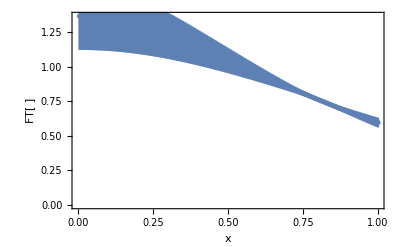

i FT[]

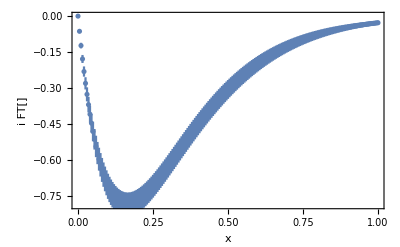

FT[] = (FT[  ]) + i (i FT[])

= FT[] = FT[  ] - FT[]

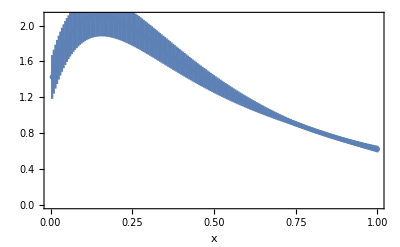

FT[] =

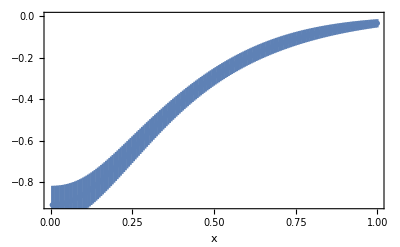

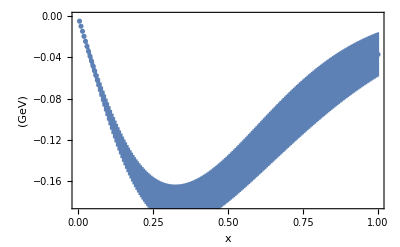

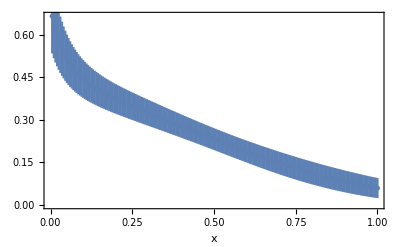

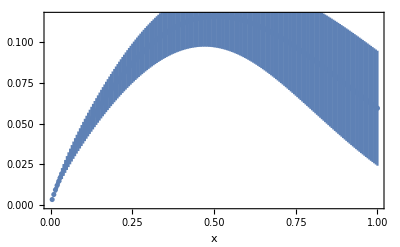

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,6, 10, 3];
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨2.42(38)⟩_(2902J), ⟨0.201(89)⟩_(2902J), ⟨0.040(11)⟩_(2902J), ⟨0.511(17)⟩_(2902J), ⟨-5.06(29)⟩_(2902J), ⟨-4.53(13)⟩_(2902J), ⟨3.10(46)⟩_(2902J)} | 1.36736

Fix f = 0.51122; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨2.44(22)⟩_(2902J), ⟨0.199(89)⟩_(2902J), ⟨0.040(11)⟩_(2902J), ⟨-5.08(25)⟩_(2902J), ⟨-4.54(11)⟩_(2902J), ⟨3.11(45)⟩_(2902J)} | 1.39846
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.215(29)⟩_(2902J), ⟨0.0306(33)⟩_(2902J), ⟨0.0306(33)⟩_(2902J)} | 2.33676
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.51(17)⟩_(2902J), ⟨0.040(41)⟩_(2902J), ⟨0.040(41)⟩_(2902J), ⟨1.97(76)⟩_(2902J)} | 1.36334

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
 FT[  ] | ⟨2.260(44)⟩_(2902J) | ⟨2.161(89)⟩_(2902J) | ⟨1.080(45)⟩_(2902J)
i FT[] |                 -15
⟨-596.5(90) × 10   ⟩_(2902J) |                -15
⟨225.5(41) × 10   ⟩_(2902J) | ⟨-0.537(34)⟩_(2902J)
= = FT[] | ⟨2.260(44)⟩_(2902J) | ⟨2.161(89)⟩_(2902J) | ⟨1.618(58)⟩_(2902J)
= = FT[] | ⟨-0.584(54)⟩_(2902J) | ⟨-0.584(54)⟩_(2902J) | ⟨-0.292(27)⟩_(2902J)
 | ⟨0.278(26)⟩_(2902J) | ⟨0.290(30)⟩_(2902J) | ⟨0.194(20)⟩_(2902J)

FT[  ]

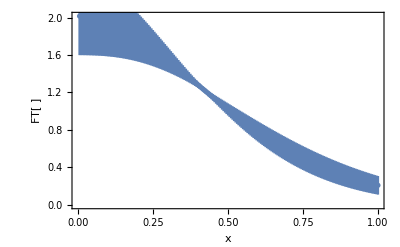

i FT[]

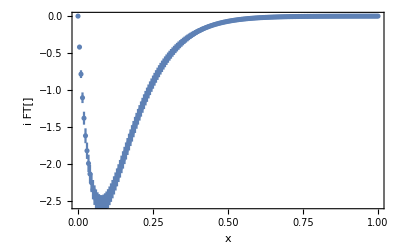

FT[] = (FT[  ]) + i (i FT[])

= FT[] = FT[  ] - FT[]

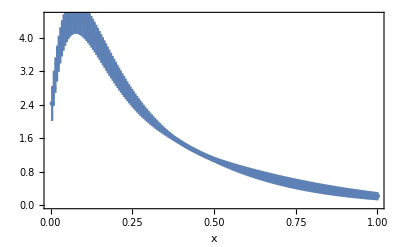

FT[] =

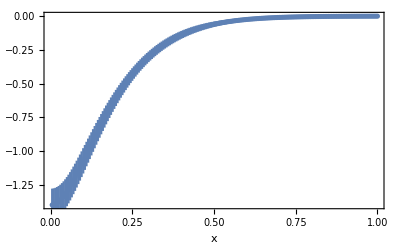

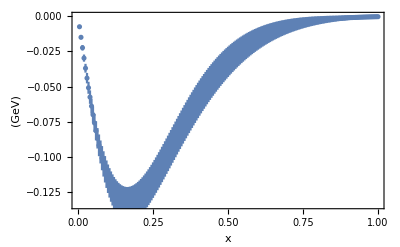

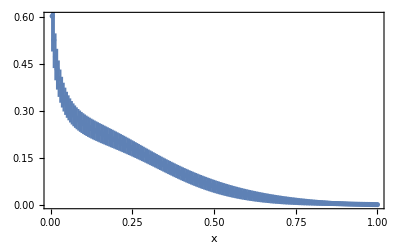

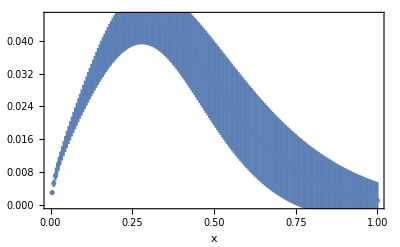

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,5, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

2.8 are SELECTED for fit!

410 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.63(23)⟩_(2902J), ⟨0.134(64)⟩_(2902J), ⟨0.032(14)⟩_(2902J), ⟨0.451(16)⟩_(2902J), ⟨-3.80(51)⟩_(2902J), ⟨-3.93(24)⟩_(2902J), ⟨3.8(12)⟩_(2902J)} | 1.66245

Fix f = 0.451384; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.64(14)⟩_(2902J), ⟨0.130(69)⟩_(2902J), ⟨0.032(13)⟩_(2902J), ⟨-3.81(51)⟩_(2902J), ⟨-3.94(24)⟩_(2902J), ⟨3.8(11)⟩_(2902J)} | 1.68166
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.208(28)⟩_(2902J), ⟨0.0373(39)⟩_(2902J), ⟨0.0373(39)⟩_(2902J)} | 1.57915
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.223(70)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨1.6(28)⟩_(2902J)} | 0.885999

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
 FT[  ] | ⟨1.414(46)⟩_(2902J) | ⟨1.412(47)⟩_(2902J) | ⟨0.706(24)⟩_(2902J)
i FT[] |                 -15
⟨-140.5(69) × 10   ⟩_(2902J) |               -15
⟨78.6(27) × 10   ⟩_(2902J) | ⟨-0.438(34)⟩_(2902J)
= = FT[] | ⟨1.414(46)⟩_(2902J) | ⟨1.412(47)⟩_(2902J) | ⟨1.144(41)⟩_(2902J)
= = FT[] | ⟨-0.284(44)⟩_(2902J) | ⟨-0.284(44)⟩_(2902J) | ⟨-0.142(22)⟩_(2902J)
 | ⟨0.216(34)⟩_(2902J) | ⟨0.217(34)⟩_(2902J) | ⟨0.134(22)⟩_(2902J)

FT[  ]

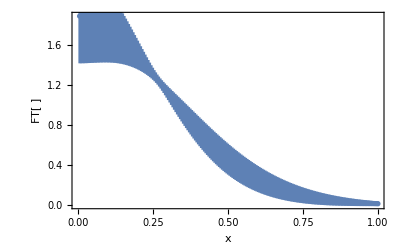

i FT[]

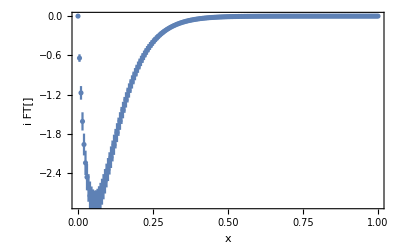

FT[] = (FT[  ]) + i (i FT[])

= FT[] = FT[  ] - FT[]

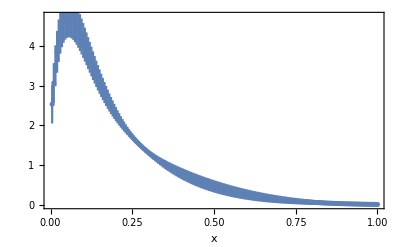

FT[] =

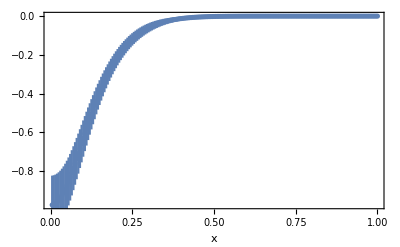

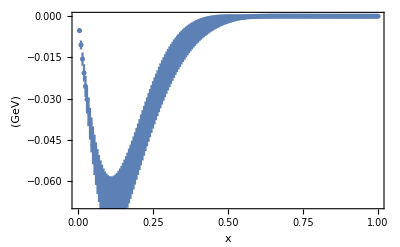

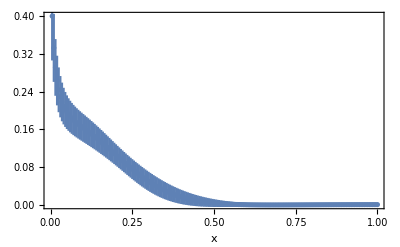

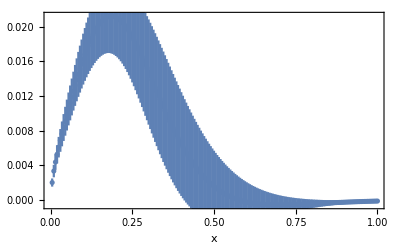

{{-4,⟨0.786(34)⟩_(RowBox[{)},{-3,⟨0.540(12)⟩_(RowBox[{)},{-2,⟨0.2944(36)⟩_(RowBox[{)},{-1,⟨0.09077(75)⟩_(RowBox[{)}}

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,4, 10, 2.8];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

```mathematica
i1 = "⟨0.294(36)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)"
i2="⟨0.278(26)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)"
i3="⟨0.216(34)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)"
```

⟨0.294(36)⟩_(RowBox[{)

⟨0.278(26)⟩_(RowBox[{)

⟨0.216(34)⟩_(RowBox[{)

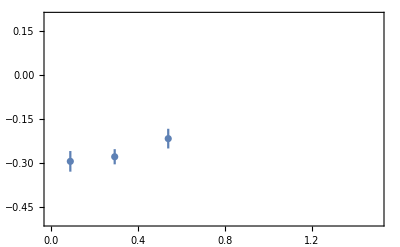

```mathematica
zetaxintegral ={{0.09077,-i1}, {0.2944,-i2},{0.540, -i3}};
ErrorListPlot[MakeErrBars[zetaxintegral],FrameLabel->{"", ""}, Frame->True , PlotRange->{{0,1.5},{0.2,-0.5}}]
```

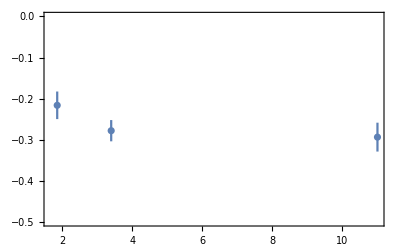

```mathematica
zetaxintegral ={{1/0.09077,-i1}, {1/0.2944,-i2},{1/0.540, -i3}};
ErrorListPlot[MakeErrBars[zetaxintegral],FrameLabel->{"", ""}, Frame->True , PlotRange->{0,-0.5}]
```

3 are SELECTED for fit!

310 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.38(18)⟩_(2902J), ⟨0.023(16)⟩_(2902J), ⟨0.0074(51)⟩_(2902J), ⟨0.548(21)⟩_(2902J), ⟨-3.00(49)⟩_(2902J), ⟨-3.44(30)⟩_(2902J), ⟨6.2(48)⟩_(2902J)} | 1.71799

Fix f = 0.547997; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.391(99)⟩_(2902J), ⟨0.022(17)⟩_(2902J), ⟨0.0074(50)⟩_(2902J), ⟨-3.02(49)⟩_(2902J), ⟨-3.45(31)⟩_(2902J), ⟨6.3(47)⟩_(2902J)} | 1.74188
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.250(27)⟩_(2902J), ⟨0.0286(24)⟩_(2902J), ⟨0.0286(24)⟩_(2902J)} | 1.39497
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.228(57)⟩_(2902J), ⟨0.013(18)⟩_(2902J), ⟨0.013(18)⟩_(2902J), ⟨1.5(30)⟩_(2902J)} | 0.747751

Infinity

=9

{a,b}-> | {-Infinity, Infinity} | {-1, +1} | {0, +1}
 FT[  ] | ⟨1.913(53)⟩_(2902J) | ⟨1.913(53)⟩_(2902J) | ⟨0.956(27)⟩_(2902J)
i FT[] |                -15
⟨130.5(98) × 10   ⟩_(2902J) |                -15
⟨239.8(42) × 10   ⟩_(2902J) | ⟨-0.659(42)⟩_(2902J)
= = FT[] | ⟨1.913(53)⟩_(2902J) | ⟨1.913(53)⟩_(2902J) | ⟨1.615(50)⟩_(2902J)
= = FT[] | ⟨-0.346(50)⟩_(2902J) | ⟨-0.346(50)⟩_(2902J) | ⟨-0.173(25)⟩_(2902J)
 | ⟨0.195(29)⟩_(2902J) | ⟨0.194(29)⟩_(2902J) | ⟨0.115(18)⟩_(2902J)

FT[  ]

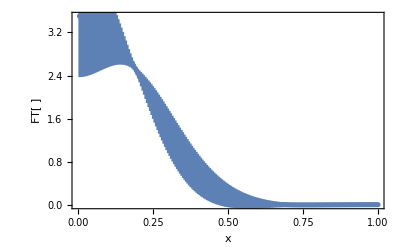

i FT[]

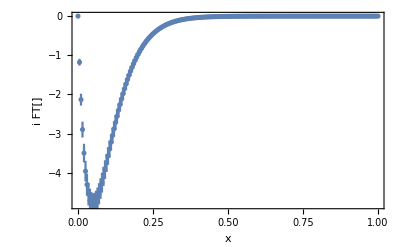

FT[] = (FT[  ]) + i (i FT[])

= FT[] = FT[  ] - FT[]

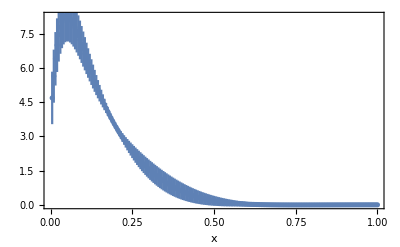

FT[] =

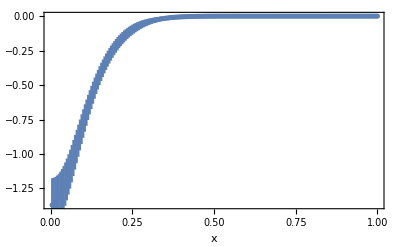

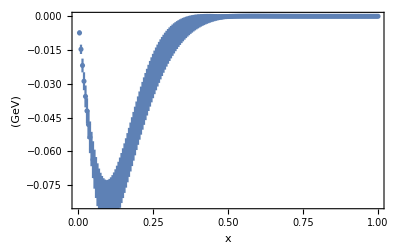

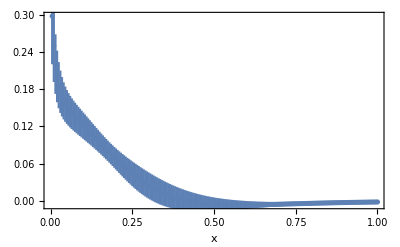

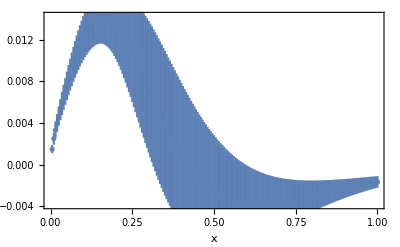

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,3, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

2 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨10.4(58)⟩_(2902J), ⟨0.78(41)⟩_(2902J), ⟨0.78(41)⟩_(2902J), ⟨0.3718(80)⟩_(2902J), ⟨-9.27(94)⟩_(2902J), ⟨-6.80(37)⟩_(2902J), ⟨1.626(98)⟩_(2902J)} | 6.13779

Fix f = 0.37182; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨11.4(42)⟩_(2902J), ⟨0.83(33)⟩_(2902J), ⟨0.83(33)⟩_(2902J), ⟨-9.25(44)⟩_(2902J), ⟨-6.79(19)⟩_(2902J), ⟨1.627(82)⟩_(2902J)} | 6.20923
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.242(25)⟩_(2902J), ⟨0.0728(60)⟩_(2902J), ⟨0.0728(60)⟩_(2902J)} | 3.21609
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.96(20)⟩_(2902J), ⟨0.152(66)⟩_(2902J), ⟨0.152(66)⟩_(2902J), ⟨2.03(33)⟩_(2902J)} | 2.05458

Infinity

=9

FT[  ]

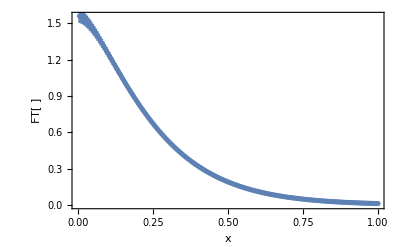

i FT[]

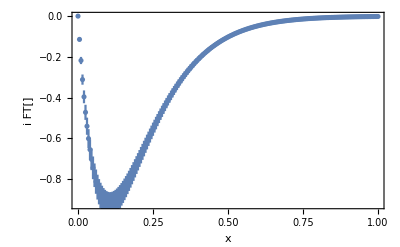

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

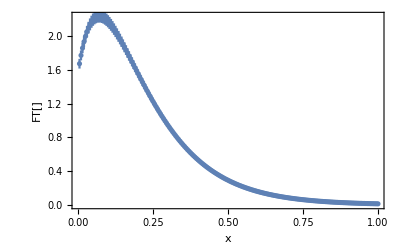

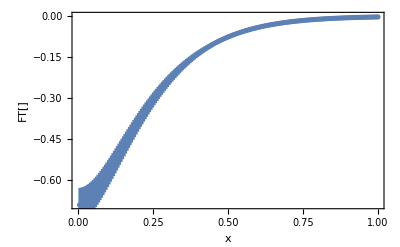

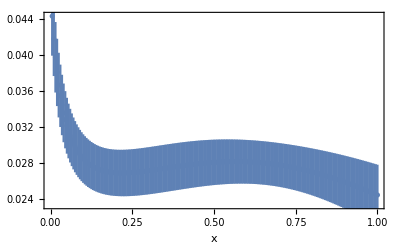

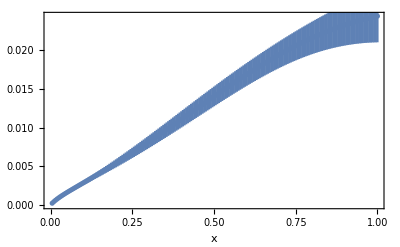

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,6, 10, 2];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨3.12(79)⟩_(2902J), ⟨0.19(16)⟩_(2902J), ⟨0.045(19)⟩_(2902J), ⟨0.519(23)⟩_(2902J), ⟨-5.80(87)⟩_(2902J), ⟨-4.84(34)⟩_(2902J), ⟨3.15(67)⟩_(2902J)} | 1.02347

Fix f = 0.518924; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨3.18(48)⟩_(2902J), ⟨0.19(16)⟩_(2902J), ⟨0.045(18)⟩_(2902J), ⟨-5.84(86)⟩_(2902J), ⟨-4.86(33)⟩_(2902J), ⟨3.16(66)⟩_(2902J)} | 1.04211
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.266(57)⟩_(2902J), ⟨0.0362(60)⟩_(2902J), ⟨0.0362(60)⟩_(2902J)} | 1.60047
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.53(26)⟩_(2902J), ⟨0.021(48)⟩_(2902J), ⟨0.021(48)⟩_(2902J), ⟨1.8(15)⟩_(2902J)} | 1.10422

Infinity

=9

FT[  ]

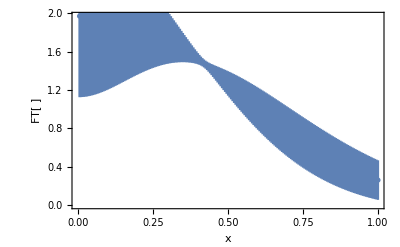

i FT[]

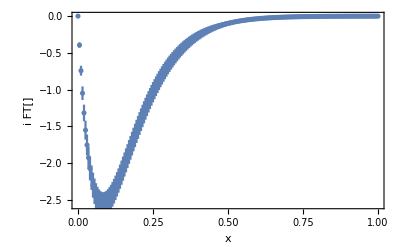

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

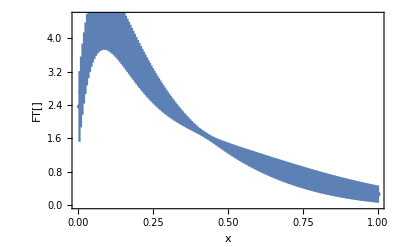

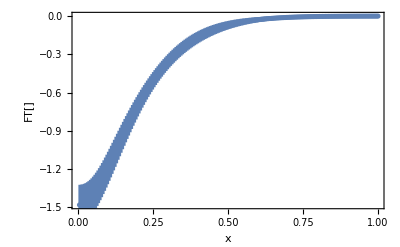

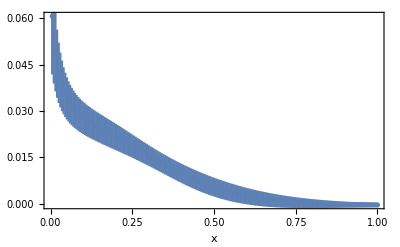

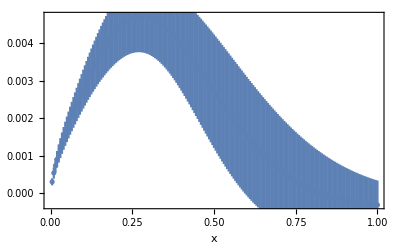

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨2.42(38)⟩_(2902J), ⟨0.201(89)⟩_(2902J), ⟨0.040(11)⟩_(2902J), ⟨0.511(17)⟩_(2902J), ⟨-5.06(29)⟩_(2902J), ⟨-4.53(13)⟩_(2902J), ⟨3.10(46)⟩_(2902J)} | 1.36736

Fix f = 0.51122; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨2.44(22)⟩_(2902J), ⟨0.199(89)⟩_(2902J), ⟨0.040(11)⟩_(2902J), ⟨-5.08(25)⟩_(2902J), ⟨-4.54(11)⟩_(2902J), ⟨3.11(45)⟩_(2902J)} | 1.39846
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.215(29)⟩_(2902J), ⟨0.0306(33)⟩_(2902J), ⟨0.0306(33)⟩_(2902J)} | 2.33676
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.51(17)⟩_(2902J), ⟨0.040(41)⟩_(2902J), ⟨0.040(41)⟩_(2902J), ⟨1.97(76)⟩_(2902J)} | 1.36334

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

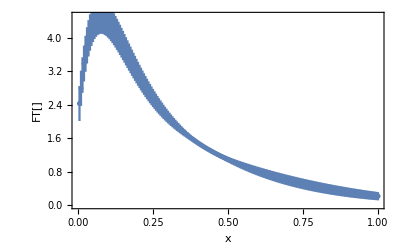

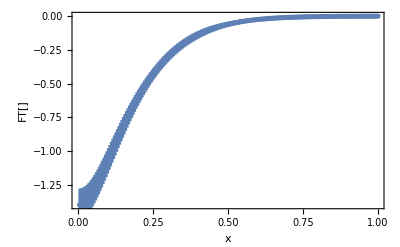

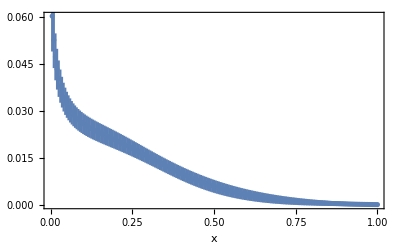

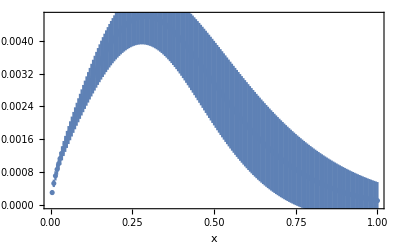

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,5, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨3.12(79)⟩_(2902J), ⟨0.19(16)⟩_(2902J), ⟨0.045(19)⟩_(2902J), ⟨0.519(23)⟩_(2902J), ⟨-5.80(87)⟩_(2902J), ⟨-4.84(34)⟩_(2902J), ⟨3.15(67)⟩_(2902J)} | 1.02347

Fix f = 0.518924; All data is divided by

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨3.18(48)⟩_(2902J), ⟨0.19(16)⟩_(2902J), ⟨0.045(18)⟩_(2902J), ⟨-5.84(86)⟩_(2902J), ⟨-4.86(33)⟩_(2902J), ⟨3.16(66)⟩_(2902J)} | 1.04211
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.266(57)⟩_(2902J), ⟨0.0362(60)⟩_(2902J), ⟨0.0362(60)⟩_(2902J)} | 1.60047
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.54(18)⟩_(2902J), ⟨0.040(40)⟩_(2902J), ⟨0.040(40)⟩_(2902J), ⟨1.97(76)⟩_(2902J)} | 1.36059

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

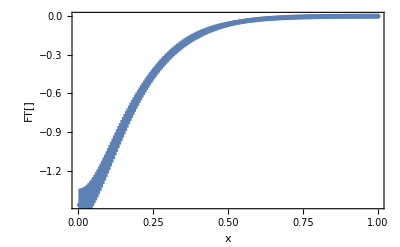

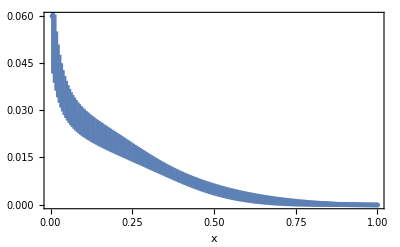

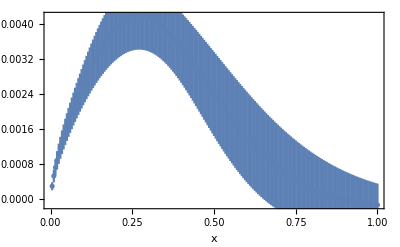

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

3 are SELECTED for fit!

49 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.52(29)⟩_(2902J), ⟨0.056(44)⟩_(2902J), ⟨0.0113(81)⟩_(2902J), ⟨0.524(27)⟩_(2902J), ⟨-4.08(54)⟩_(2902J), ⟨-4.04(27)⟩_(2902J), ⟨5.3(39)⟩_(2902J)} | 1.3656

Fix f = 0.523549; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.54(15)⟩_(2902J), ⟨0.054(46)⟩_(2902J), ⟨0.0113(80)⟩_(2902J), ⟨-4.10(52)⟩_(2902J), ⟨-4.05(27)⟩_(2902J), ⟨5.3(39)⟩_(2902J)} | 1.37205
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.244(39)⟩_(2902J), ⟨0.0314(39)⟩_(2902J), ⟨0.0314(39)⟩_(2902J)} | 1.31313
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.199(61)⟩_(2902J), ⟨0.002 ± 0.017⟩_(2902J), ⟨0.002 ± 0.017⟩_(2902J), ⟨-59(26)⟩_(2902J)} | 0.736206

Infinity

=9

FT[  ]

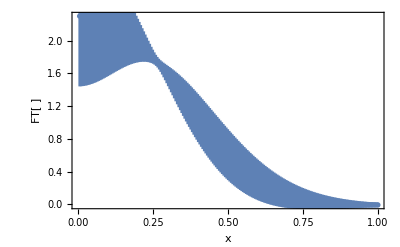

i FT[]

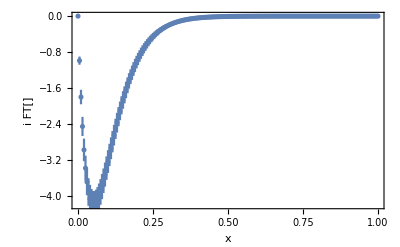

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

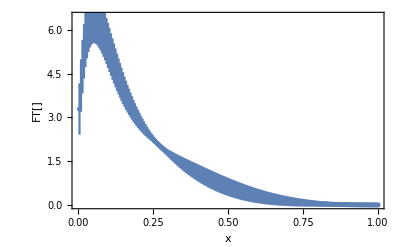

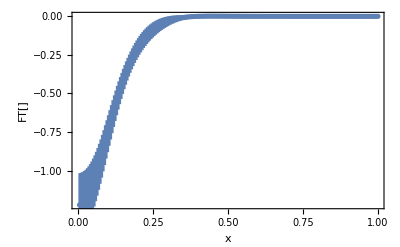

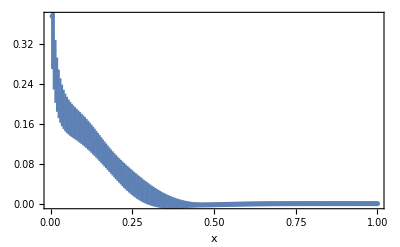

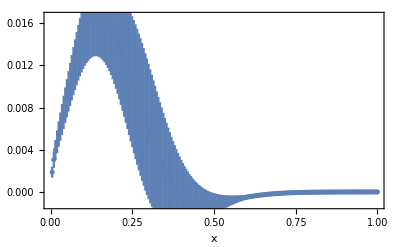

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,4, 9, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

2.8 are SELECTED for fit!

49 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.64(22)⟩_(2902J), ⟨0.125(62)⟩_(2902J), ⟨0.032(14)⟩_(2902J), ⟨0.453(16)⟩_(2902J), ⟨-3.73(58)⟩_(2902J), ⟨-3.90(28)⟩_(2902J), ⟨3.8(11)⟩_(2902J)} | 1.81791

Fix f = 0.452545; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.65(14)⟩_(2902J), ⟨0.122(66)⟩_(2902J), ⟨0.032(13)⟩_(2902J), ⟨-3.74(58)⟩_(2902J), ⟨-3.91(28)⟩_(2902J), ⟨3.8(11)⟩_(2902J)} | 1.83696
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.209(28)⟩_(2902J), ⟨0.0373(38)⟩_(2902J), ⟨0.0373(38)⟩_(2902J)} | 1.67943
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.223(68)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨1.6(29)⟩_(2902J)} | 0.917363

Infinity

=9

FT[  ]

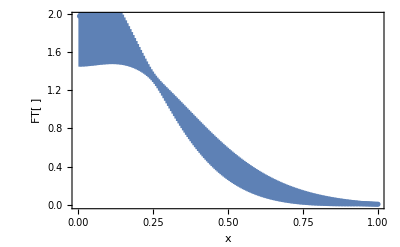

i FT[]

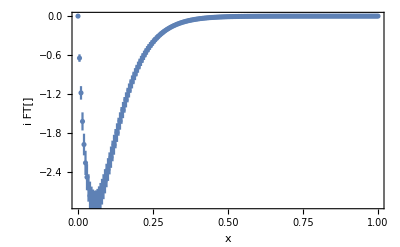

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

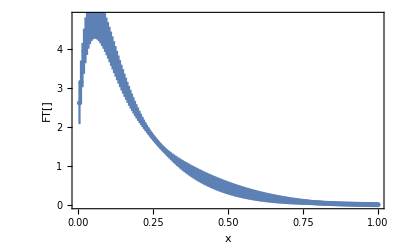

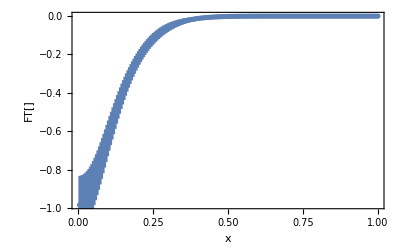

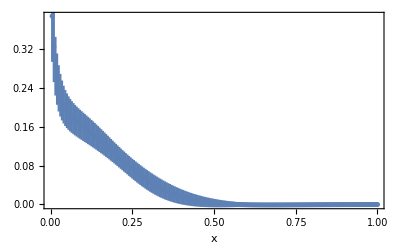

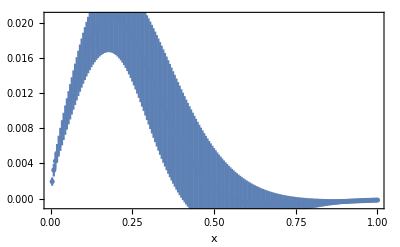

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,4, 9, 2.8];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

2.8 are SELECTED for fit!

310 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.47(13)⟩_(2902J), ⟨0.072(27)⟩_(2902J), ⟨0.0251(74)⟩_(2902J), ⟨0.472(13)⟩_(2902J), ⟨-2.69(44)⟩_(2902J), ⟨-3.31(25)⟩_(2902J), ⟨3.96(84)⟩_(2902J)} | 2.60568

Fix f = 0.47161; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.474(75)⟩_(2902J), ⟨0.071(29)⟩_(2902J), ⟨0.0251(72)⟩_(2902J), ⟨-2.70(46)⟩_(2902J), ⟨-3.32(26)⟩_(2902J), ⟨3.97(81)⟩_(2902J)} | 2.65535
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.205(20)⟩_(2902J), ⟨0.0317(23)⟩_(2902J), ⟨0.0317(23)⟩_(2902J)} | 1.81804
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.255(70)⟩_(2902J), ⟨0.031(28)⟩_(2902J), ⟨0.031(28)⟩_(2902J), ⟨2.1(11)⟩_(2902J)} | 0.930133

Infinity

=9

FT[  ]

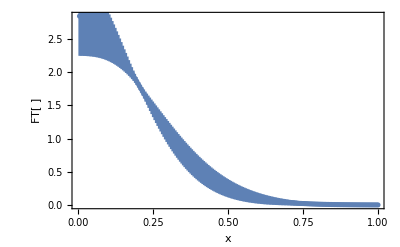

i FT[]

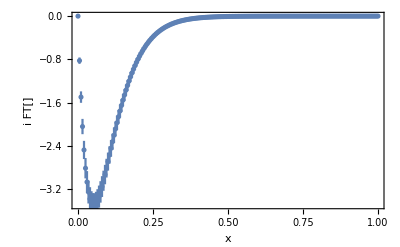

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

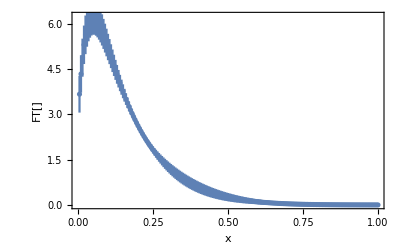

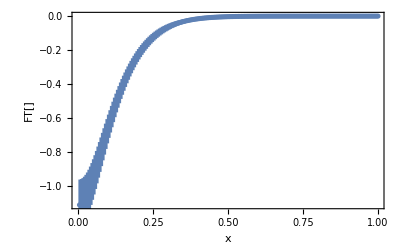

-Graphics-

-Graphics-

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,3, 10, 2.8];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,4, 10, 2.8];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

2.8 are SELECTED for fit!

410 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.63(23)⟩_(2902J), ⟨0.134(64)⟩_(2902J), ⟨0.032(14)⟩_(2902J), ⟨0.451(16)⟩_(2902J), ⟨-3.80(51)⟩_(2902J), ⟨-3.93(24)⟩_(2902J), ⟨3.8(12)⟩_(2902J)} | 1.66245

Fix f = 0.451384; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.64(14)⟩_(2902J), ⟨0.130(69)⟩_(2902J), ⟨0.032(13)⟩_(2902J), ⟨-3.81(51)⟩_(2902J), ⟨-3.94(24)⟩_(2902J), ⟨3.8(11)⟩_(2902J)} | 1.68166
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.208(28)⟩_(2902J), ⟨0.0373(39)⟩_(2902J), ⟨0.0373(39)⟩_(2902J)} | 1.57915
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.223(70)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨0.017(26)⟩_(2902J), ⟨1.6(28)⟩_(2902J)} | 0.885999

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,5, 10, 2.8];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

2.8 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.74(39)⟩_(2902J), ⟨0.17(12)⟩_(2902J), ⟨0.031(22)⟩_(2902J), ⟨0.440(21)⟩_(2902J), ⟨-4.67(85)⟩_(2902J), ⟨-4.35(36)⟩_(2902J), ⟨3.7(19)⟩_(2902J)} | 1.19724

Fix f = 0.440418; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.77(27)⟩_(2902J), ⟨0.16(13)⟩_(2902J), ⟨0.032(22)⟩_(2902J), ⟨-4.67(84)⟩_(2902J), ⟨-4.36(36)⟩_(2902J), ⟨3.7(19)⟩_(2902J)} | 1.20331
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.212(42)⟩_(2902J), ⟨0.0438(67)⟩_(2902J), ⟨0.0438(67)⟩_(2902J)} | 1.20667
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.198(77)⟩_(2902J), ⟨0.005 ± 0.029⟩_(2902J), ⟨0.005 ± 0.029⟩_(2902J), ⟨-7.1(84)⟩_(2902J)} | 0.827421

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,2, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

210 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.147(89)⟩_(2902J), ⟨0.0073(68)⟩_(2902J), ⟨0.0025(32)⟩_(2902J), ⟨0.558(15)⟩_(2902J), ⟨-2.18(19)⟩_(2902J), ⟨-2.87(16)⟩_(2902J), ⟨-3. ± 20.⟩_(2902J)} | 2.27077

Fix f = 0.558065; All data is divided by

$Aborted

$Aborted

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,4, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

410 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.50(29)⟩_(2902J), ⟨0.063(48)⟩_(2902J), ⟨0.0112(81)⟩_(2902J), ⟨0.520(28)⟩_(2902J), ⟨-4.11(47)⟩_(2902J), ⟨-4.05(24)⟩_(2902J), ⟨5.3(40)⟩_(2902J)} | 1.25407

Fix f = 0.519895; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.52(15)⟩_(2902J), ⟨0.060(50)⟩_(2902J), ⟨0.0112(80)⟩_(2902J), ⟨-4.13(45)⟩_(2902J), ⟨-4.06(23)⟩_(2902J), ⟨5.3(39)⟩_(2902J)} | 1.26171
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.239(38)⟩_(2902J), ⟨0.0313(39)⟩_(2902J), ⟨0.0313(39)⟩_(2902J)} | 1.2472
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.195(61)⟩_(2902J), ⟨0.001 ± 0.017⟩_(2902J), ⟨0.001 ± 0.017⟩_(2902J), ⟨-62(26)⟩_(2902J)} | 0.715586

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,5, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.50(43)⟩_(2902J), ⟨0.072(91)⟩_(2902J), ⟨0.009 ± 0.011⟩_(2902J), ⟨0.503(37)⟩_(2902J), ⟨-5.07(72)⟩_(2902J), ⟨-4.50(33)⟩_(2902J), ⟨1.8(84)⟩_(2902J)} | 0.989156

Fix f = 0.502992; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.54(22)⟩_(2902J), ⟨0.068(93)⟩_(2902J), ⟨0.009 ± 0.011⟩_(2902J), ⟨-5.09(70)⟩_(2902J), ⟨-4.51(32)⟩_(2902J), ⟨1.8(83)⟩_(2902J)} | 0.992043
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} |                 9                                              3                                             3
{⟨-9.44(73) × 10 ⟩_(2902J), ⟨2.70(21) × 10 ⟩_(2902J), ⟨268(21) × 10 ⟩_(2902J)} | 138.695
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} |                                                                                                                                                   3
{⟨0.166(47)⟩_(2902J), ⟨-0.0025(18)⟩_(2902J), ⟨-0.0025(18)⟩_(2902J), ⟨-22.6(33) × 10 ⟩_(2902J)} | 0.687651

Infinity

=9

$Aborted

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.32(58)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨0.482(47)⟩_(2902J), ⟨-6.09(60)⟩_(2902J), ⟨-4.93(26)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.791047

Fix f = 0.481945; All data is divided by

510 are SELECTED for fit!

2 are SELECTED for only A12B fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.40(29)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨-6.10(58)⟩_(2902J), ⟨-4.94(25)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.7933
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.165(71)⟩_(2902J), ⟨0.033(11)⟩_(2902J), ⟨0.033(11)⟩_(2902J)} | 0.731663
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.76(26)⟩_(2902J), ⟨0.082(72)⟩_(2902J), ⟨0.082(72)⟩_(2902J), ⟨2.03(76)⟩_(2902J)} | 0.98839

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.32(58)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨0.482(47)⟩_(2902J), ⟨-6.09(60)⟩_(2902J), ⟨-4.93(26)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.791047

Fix f = 0.481945; All data is divided by

510 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.40(29)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨-6.10(58)⟩_(2902J), ⟨-4.94(25)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.7933
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.165(71)⟩_(2902J), ⟨0.033(11)⟩_(2902J), ⟨0.033(11)⟩_(2902J)} | 0.731663
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} |                                                                                                                                           3
{⟨-11(11)⟩_(2902J), ⟨-3.5(35)⟩_(2902J), ⟨-3.5(35)⟩_(2902J), ⟨133.5(35) × 10 ⟩_(2902J)} | 0.981203

Infinity

=9

$Aborted

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨3.12(79)⟩_(2902J), ⟨0.19(16)⟩_(2902J), ⟨0.045(19)⟩_(2902J), ⟨0.519(23)⟩_(2902J), ⟨-5.80(87)⟩_(2902J), ⟨-4.84(34)⟩_(2902J), ⟨3.15(67)⟩_(2902J)} | 1.02347

Fix f = 0.518924; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨3.18(48)⟩_(2902J), ⟨0.19(16)⟩_(2902J), ⟨0.045(18)⟩_(2902J), ⟨-5.84(86)⟩_(2902J), ⟨-4.86(33)⟩_(2902J), ⟨3.16(66)⟩_(2902J)} | 1.04211
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.266(57)⟩_(2902J), ⟨0.0362(60)⟩_(2902J), ⟨0.0362(60)⟩_(2902J)} | 1.60047
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.53(26)⟩_(2902J), ⟨0.021(48)⟩_(2902J), ⟨0.021(48)⟩_(2902J), ⟨1.8(15)⟩_(2902J)} | 1.10422

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2B = GiveParaFitA12BA2B[-1,6, 10, 3];
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨4.01(58)⟩_(2902J), ⟨0.43(17)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.496(12)⟩_(2902J), ⟨-5.81(33)⟩_(2902J), ⟨-4.86(14)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.56911

Fix f = 0.495923; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨4.03(40)⟩_(2902J), ⟨0.43(17)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨-5.83(30)⟩_(2902J), ⟨-4.86(12)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.62298
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.153(31)⟩_(2902J), ⟨0.0345(56)⟩_(2902J), ⟨0.0345(56)⟩_(2902J)} | 1.47336
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.64(18)⟩_(2902J), ⟨0.041(34)⟩_(2902J), ⟨0.041(34)⟩_(2902J), ⟨1.99(71)⟩_(2902J)} | 1.14898

```mathematica
PrintxA2B[ParaFitA12BA2B,-1, 9]
```

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨3.12(79)⟩_(2902J), ⟨0.19(16)⟩_(2902J), ⟨0.045(19)⟩_(2902J), ⟨0.519(23)⟩_(2902J), ⟨-5.80(87)⟩_(2902J), ⟨-4.84(34)⟩_(2902J), ⟨3.15(67)⟩_(2902J)} | 1.02347

Fix f = 0.518924; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨3.18(48)⟩_(2902J), ⟨0.19(16)⟩_(2902J), ⟨0.045(18)⟩_(2902J), ⟨-5.84(86)⟩_(2902J), ⟨-4.86(33)⟩_(2902J), ⟨3.16(66)⟩_(2902J)} | 1.04211
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.266(57)⟩_(2902J), ⟨0.0362(60)⟩_(2902J), ⟨0.0362(60)⟩_(2902J)} | 1.60047
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.54(18)⟩_(2902J), ⟨0.040(40)⟩_(2902J), ⟨0.040(40)⟩_(2902J), ⟨1.97(76)⟩_(2902J)} | 1.36059

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.32(58)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨0.482(47)⟩_(2902J), ⟨-6.09(60)⟩_(2902J), ⟨-4.93(26)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.791047

Fix f = 0.481945; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.40(29)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨-6.10(58)⟩_(2902J), ⟨-4.94(25)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.7933
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.165(71)⟩_(2902J), ⟨0.033(11)⟩_(2902J), ⟨0.033(11)⟩_(2902J)} | 0.731663
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.161(50)⟩_(2902J), ⟨0.001 ± 0.017⟩_(2902J), ⟨0.001 ± 0.017⟩_(2902J), ⟨-68(28)⟩_(2902J)} | 0.756106

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.32(58)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨0.482(47)⟩_(2902J), ⟨-6.09(60)⟩_(2902J), ⟨-4.93(26)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.791047

Fix f = 0.481945; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.40(29)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨-6.10(58)⟩_(2902J), ⟨-4.94(25)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.7933
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.165(71)⟩_(2902J), ⟨0.033(11)⟩_(2902J), ⟨0.033(11)⟩_(2902J)} | 0.731663
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.160(52)⟩_(2902J), ⟨0.001 ± 0.018⟩_(2902J), ⟨0.001 ± 0.018⟩_(2902J), ⟨-70(28)⟩_(2902J)} | 0.735644

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.32(58)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨0.482(47)⟩_(2902J), ⟨-6.09(60)⟩_(2902J), ⟨-4.93(26)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.791047

Fix f = 0.481945; All data is divided by

2 are SELECTED for only A12B fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.40(29)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨-6.10(58)⟩_(2902J), ⟨-4.94(25)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.7933
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.165(71)⟩_(2902J), ⟨0.033(11)⟩_(2902J), ⟨0.033(11)⟩_(2902J)} | 0.731663
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} | {⟨0.89(38)⟩_(2902J), ⟨0.073(91)⟩_(2902J), ⟨0.073(91)⟩_(2902J), ⟨1.9(11)⟩_(2902J)} | 0.923342

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP4 = GiveParaFitA12BA2B[-4,6, 10, 1];
PrintxA2B[ParaFitA12BA2BP4,-4, 9]
```

1 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨2.12(34)⟩_(2902J), ⟨2.50(96)⟩_(2902J), ⟨0.46(15)⟩_(2902J), ⟨0.1767(73)⟩_(2902J), ⟨-5.28(38)⟩_(2902J), ⟨-4.81(13)⟩_(2902J), ⟨2.28(34)⟩_(2902J)} | 1.52698

Fix f = 0.176656; All data is divided by

2 are SELECTED for only A12B fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨2.13(28)⟩_(2902J), ⟨2.5(11)⟩_(2902J), ⟨0.46(15)⟩_(2902J), ⟨-5.28(39)⟩_(2902J), ⟨-4.81(13)⟩_(2902J), ⟨2.28(34)⟩_(2902J)} | 1.52841
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.122(45)⟩_(2902J), ⟨0.152(58)⟩_(2902J), ⟨0.152(58)⟩_(2902J)} | 0.993178
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} |                    3 - MantissaExponent[??][[2]]                                                                                                                                           3 - MantissaExponent[??][[2]]                                                                                                                                           3 - MantissaExponent[??][[2]]                                                                                                                                           3 - MantissaExponent[??][[2]]
{{⟨If[Sign[Round[10                              a]] == -1, -, ]<>        3 - MantissaExponent[??][[2]]    <>IntegerDigits[??]<>1<>2<>)⟩_(1J), {}}, {⟨If[Sign[Round[10                              c]] == -1, -, ]<>        3 - MantissaExponent[??][[2]]    <>IntegerDigits[??]<>1<>2<>)⟩_(1J), {}}, {⟨If[Sign[Round[10                              d]] == -1, -, ]<>        3 - MantissaExponent[??][[2]]    <>IntegerDigits[??]<>1<>2<>)⟩_(1J), {}}, {⟨If[Sign[Round[10                              nparam]] == -1, -, ]<>        3 - MantissaExponent[??][[2]]         <>IntegerDigits[??]<>1<>2<>)⟩_(1J), {}}}
                                                                  Round[10                              a](                                                                                                                               Round[10                              c](                                                                                                                               Round[10                              d](                                                                                                                                    Round[10                              nparam]( |                               2                                 2                                 2                                 2                                 2                                2                                 2                                  2                                 2                                   2                                   2                                  2                                   2                                  2                                   2                                  2                                  2                                  2                                  2                                 2                                   2                                  2                                  2                                  2                                  2                                  2                                  2                                 2                                  2                                  2                                   2                                  2                                  2                                  2                                  2                                   2                                  2                                  2                                  2                                   2                                   2                                  2                                 2                                  2                                  2                                  2                                   2                                 2                                  2                                 2                                   2                                   2                                   2                                  2                                  2                                   2                                 2                                  2                                  2                                   2                                  2                                  2                                  2                                  2                                  2                                  2                                 2                                  2                                  2                                  2                                  2                                   2                                   2                                  2                                  2                                  2                                   2                                  2                                  2                                  2                                  2                                  2                                  2                                   2                                   2                                   2                                   2                                    2                                   2                                    2                                   2                                    2                                   2                                    2                                   2                                    2                                   2                                    2                                    2                                     2                                   2                                  2                                  2                                   2                                  2                                   2                                  2                                   2                                   2                                  2                                   2                                  2                                 2                                  2                                  2                                  2                                  2                                  2                                2                                  2                                 2                                  2                                  2                                 2                                 2                                 2                                2                                 2                                  2                                 2                                 2                                  2                                  2                                  2                                  2                                 2                               2                                  2                                 2                                  2                                 2                                 2                                 2                                 2                                  2                              2                                 2                                 2                                2                                2                                  2                                2                                  2                                2                                2                                2                                2                                2                                 2                                2                               2                                2                                 2                               2                                 2                                2                                2                                2                                2                                2                               2                               2                                 2                                2                                 2                                2                                2                                2                                2                                2
1.99976 (-0.0268873 + {}[[2]])  + 1.99743 (-0.0242067 + {}[[2]])  + 1.99967 (-0.0206121 + {}[[2]])  + 1.99979 (-0.0167367 + {}[[2]])  + 1.99959 (-0.0162212 + {}[[2]])  + 0.999939 (-0.01102 + {}[[2]])  + 1.99987 (-0.0108958 + {}[[2]])  + 1.99982 (-0.00999256 + {}[[2]])  + 1.9998 (-0.00990753 + {}[[2]])  + 0.999921 (-0.00953215 + {}[[2]])  + 0.999959 (-0.00906612 + {}[[2]])  + 1.99992 (-0.00893891 + {}[[2]])  + 0.999952 (-0.00861697 + {}[[2]])  + 1.99997 (-0.00848655 + {}[[2]])  + 0.999969 (-0.00833834 + {}[[2]])  + 1.99948 (-0.00810243 + {}[[2]])  + 1.99759 (-0.00794567 + {}[[2]])  + 1.99983 (-0.00780351 + {}[[2]])  + 1.99997 (-0.00756041 + {}[[2]])  + 1.9999 (-0.00725918 + {}[[2]])  + 0.999902 (-0.00697382 + {}[[2]])  + 1.99997 (-0.00684873 + {}[[2]])  + 1.99993 (-0.00683058 + {}[[2]])  + 1.99994 (-0.00651194 + {}[[2]])  + 0.999973 (-0.0064521 + {}[[2]])  + 1.99971 (-0.00632575 + {}[[2]])  + 1.99941 (-0.00629875 + {}[[2]])  + 1.9999 (-0.00590158 + {}[[2]])  + 1.99997 (-0.00586258 + {}[[2]])  + 1.99923 (-0.00537751 + {}[[2]])  + 0.999904 (-0.00528821 + {}[[2]])  + 1.99983 (-0.00514014 + {}[[2]])  + 1.99999 (-0.00509714 + {}[[2]])  + 1.99994 (-0.00488439 + {}[[2]])  + 1.99998 (-0.00486578 + {}[[2]])  + 0.999876 (-0.00475982 + {}[[2]])  + 1.99983 (-0.00468487 + {}[[2]])  + 1.99998 (-0.00452386 + {}[[2]])  + 1.99996 (-0.00425706 + {}[[2]])  + 0.999894 (-0.00411036 + {}[[2]])  + 0.999993 (-0.00409515 + {}[[2]])  + 1.99993 (-0.00404441 + {}[[2]])  + 1.99988 (-0.0039179 + {}[[2]])  + 1.99961 (-0.00374499 + {}[[2]])  + 1.99998 (-0.00352587 + {}[[2]])  + 1.99999 (-0.00342316 + {}[[2]])  + 0.999471 (-0.00331446 + {}[[2]])  + 1.9997 (-0.00328573 + {}[[2]])  + 0.999842 (-0.0032833 + {}[[2]])  + 1.99975 (-0.0030237 + {}[[2]])  + 0.999992 (-0.00299218 + {}[[2]])  + 0.999876 (-0.00298103 + {}[[2]])  + 0.999977 (-0.00295025 + {}[[2]])  + 1.99996 (-0.00294419 + {}[[2]])  + 1.99979 (-0.00288163 + {}[[2]])  + 0.999971 (-0.00287648 + {}[[2]])  + 1.99997 (-0.0027872 + {}[[2]])  + 1.99995 (-0.00259947 + {}[[2]])  + 1.99992 (-0.00259476 + {}[[2]])  + 0.999959 (-0.00247407 + {}[[2]])  + 1.99998 (-0.00247033 + {}[[2]])  + 1.99996 (-0.00242819 + {}[[2]])  + 1.99753 (-0.00236525 + {}[[2]])  + 1.99989 (-0.00235378 + {}[[2]])  + 1.99998 (-0.00199137 + {}[[2]])  + 1.99996 (-0.00186816 + {}[[2]])  + 1.99999 (-0.0017679 + {}[[2]])  + 1.99999 (-0.00176148 + {}[[2]])  + 1.99995 (-0.00175207 + {}[[2]])  + 1.99991 (-0.00170335 + {}[[2]])  + 1.99977 (-0.00156448 + {}[[2]])  + 0.999988 (-0.00155954 + {}[[2]])  + 0.999955 (-0.00140329 + {}[[2]])  + 1.99995 (-0.00134859 + {}[[2]])  + 1.99992 (-0.00126985 + {}[[2]])  + 1.99991 (-0.00124184 + {}[[2]])  + 0.999987 (-0.00121803 + {}[[2]])  + 1.99986 (-0.00121195 + {}[[2]])  + 1.99995 (-0.00119186 + {}[[2]])  + 1.99991 (-0.00112853 + {}[[2]])  + 1.99994 (-0.00112608 + {}[[2]])  + 1.99993 (-0.00104897 + {}[[2]])  + 1.99968 (-0.00103179 + {}[[2]])  + 1.99993 (-0.000978633 + {}[[2]])  + 1.99915 (-0.000787494 + {}[[2]])  + 1.99997 (-0.000769111 + {}[[2]])  + 1.99991 (-0.000758592 + {}[[2]])  + 0.999611 (-0.000655435 + {}[[2]])  + 1.99998 (-0.000646678 + {}[[2]])  + 0.999982 (-0.000570672 + {}[[2]])  + 1.99927 (-0.000468854 + {}[[2]])  + 0.999979 (-0.000455056 + {}[[2]])  + 1.99999 (-0.000388329 + {}[[2]])  + 0.999983 (-0.000368879 + {}[[2]])  + 1.99985 (-0.000347602 + {}[[2]])  + 0.999839 (-0.000343457 + {}[[2]])  + 1.99994 (-0.000317171 + {}[[2]])  + 0.999925 (-0.000315105 + {}[[2]])  + 0.999891 (-0.000232957 + {}[[2]])  + 0.999943 (-0.0000283833 + {}[[2]])  + 1.99995 (0.0000934654 + {}[[2]])  + 0.999987 (0.00011262 + {}[[2]])  + 1.99997 (0.000216496 + {}[[2]])  + 0.999974 (0.000244089 + {}[[2]])  + 0.99999 (0.000278956 + {}[[2]])  + 0.999962 (0.000354889 + {}[[2]])  + 1.99999 (0.000358979 + {}[[2]])  + 0.999984 (0.000424389 + {}[[2]])  + 0.999979 (0.000466615 + {}[[2]])  + 1.99998 (0.000711946 + {}[[2]])  + 0.999958 (0.000778709 + {}[[2]])  + 1.99993 (0.000804118 + {}[[2]])  + 0.99998 (0.00081825 + {}[[2]])  + 1.99999 (0.000833783 + {}[[2]])  + 0.999986 (0.00083477 + {}[[2]])  + 0.99998 (0.000932391 + {}[[2]])  + 1.99995 (0.000975473 + {}[[2]])  + 0.999992 (0.00102474 + {}[[2]])  + 1.99998 (0.0011664 + {}[[2]])  + 0.999993 (0.00136993 + {}[[2]])  + 1.99992 (0.00151768 + {}[[2]])  + 0.999561 (0.00171227 + {}[[2]])  + 0.999989 (0.00178366 + {}[[2]])  + 1.99998 (0.00186845 + {}[[2]])  + 1.99988 (0.00209509 + {}[[2]])  + 1.99996 (0.00213099 + {}[[2]])  + 1.9999 (0.00234631 + {}[[2]])  + 1.99965 (0.00243383 + {}[[2]])  + 0.999988 (0.00248758 + {}[[2]])  + 1.99993 (0.00253601 + {}[[2]])  + 1.99994 (0.00265638 + {}[[2]])  + 0.999908 (0.00275506 + {}[[2]])  + 0.999962 (0.00295869 + {}[[2]])  + 0.999969 (0.00306555 + {}[[2]])  + 0.999981 (0.00313023 + {}[[2]])  + 0.99998 (0.00329807 + {}[[2]])  + 1.999 (0.00332762 + {}[[2]])  + 0.999986 (0.00336804 + {}[[2]])  + 1.99866 (0.00353328 + {}[[2]])  + 0.999956 (0.00360251 + {}[[2]])  + 1.99997 (0.00383231 + {}[[2]])  + 1.99998 (0.00386331 + {}[[2]])  + 1.99986 (0.00511157 + {}[[2]])  + 1.99983 (0.00520488 + {}[[2]])  + 0.999973 (0.00546365 + {}[[2]])  + 1.9992 (0.005959 + {}[[2]])  + 1.99996 (0.00612741 + {}[[2]])  + 0.99956 (0.00651107 + {}[[2]])  + 1.99993 (0.0065403 + {}[[2]])  + 1.9995 (0.00703943 + {}[[2]])  + 0.999908 (0.00820421 + {}[[2]])  + 1.9997 (0.00874872 + {}[[2]])  + 0.999611 (0.00932914 + {}[[2]])  + 1.99949 (0.0116976 + {}[[2]])  + 1.99947 (0.0119081 + {}[[2]])  + 1.99903 (0.0122452 + {}[[2]])  + 1.99752 (0.0127264 + {}[[2]])  + 1.99915 (0.0137826 + {}[[2]])  + 0.999595 (0.0139452 + {}[[2]])  + 1.99972 (0.0142269 + {}[[2]])  + 1.9997 (0.0148075 + {}[[2]])  + 1.99952 (0.0153285 + {}[[2]])  + 0.999583 (0.0153287 + {}[[2]])  + 1.9994 (0.0158993 + {}[[2]])  + 0.999501 (0.0160591 + {}[[2]])  + 1.99761 (0.0163355 + {}[[2]])  + 1.99652 (0.0170188 + {}[[2]])  + 1.99709 (0.0178384 + {}[[2]])  + 1.99972 (0.0182353 + {}[[2]])  + 1.99938 (0.0183763 + {}[[2]])  + 1.9995 (0.0187595 + {}[[2]])  + 1.99967 (0.018936 + {}[[2]])  + 0.999597 (0.0194003 + {}[[2]])  + 1.99942 (0.0194761 + {}[[2]])  + 0.999546 (0.0260392 + {}[[2]])  + 1.99891 (0.0323063 + {}[[2]])  + 1.99749 (0.0340149 + {}[[2]])  + 1.99715 (0.0386198 + {}[[2]])  + 1.99662 (0.0497348 + {}[[2]])  + 1.99864 (0.0605655 + {}[[2]])
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                 296

Infinity

=9

$Aborted

```mathematica
ParaFitA12BA2BP4 = GiveParaFitA12BA2B[-4,6, 10, 1];
PrintxA2B[ParaFitA12BA2BP4,-4, 9]
```

1 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨2.12(34)⟩_(2902J), ⟨2.50(96)⟩_(2902J), ⟨0.46(15)⟩_(2902J), ⟨0.1767(73)⟩_(2902J), ⟨-5.28(38)⟩_(2902J), ⟨-4.81(13)⟩_(2902J), ⟨2.28(34)⟩_(2902J)} | 1.52698

Fix f = 0.176656; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨2.13(28)⟩_(2902J), ⟨2.5(11)⟩_(2902J), ⟨0.46(15)⟩_(2902J), ⟨-5.28(39)⟩_(2902J), ⟨-4.81(13)⟩_(2902J), ⟨2.28(34)⟩_(2902J)} | 1.52841
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.122(45)⟩_(2902J), ⟨0.152(58)⟩_(2902J), ⟨0.152(58)⟩_(2902J)} | 0.993178
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} |                                                           3                                                                                       3
{⟨-57.3(55)⟩_(2902J), ⟨-600(250) × 10 ⟩_(2902J), ⟨-133(13)⟩_(2902J), ⟨-5.9(34) × 10 ⟩_(2902J)} | 18.4167

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨1.32(58)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨0.482(47)⟩_(2902J), ⟨-6.09(60)⟩_(2902J), ⟨-4.93(26)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.791047

Fix f = 0.481945; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨1.40(29)⟩_(2902J), ⟨0.07 ± 0.23⟩_(2902J), ⟨0.006 ± 0.016⟩_(2902J), ⟨-6.10(58)⟩_(2902J), ⟨-4.94(25)⟩_(2902J), ⟨-17(19)⟩_(2902J)} | 0.7933
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.165(71)⟩_(2902J), ⟨0.033(11)⟩_(2902J), ⟨0.033(11)⟩_(2902J)} | 0.731663
A12B | -a (1+(c+d) b_L^2+d b_T^2)^-j | {a,c,d,j} |                                                                                                                                           3
{⟨-11(11)⟩_(2902J), ⟨-3.5(35)⟩_(2902J), ⟨-3.5(35)⟩_(2902J), ⟨133.5(35) × 10 ⟩_(2902J)} | 0.981203

Infinity

=9

$Aborted

```mathematica
GiveParaFitA12BA2B[P1_,etamin_, etamax_, bminForFit_]:=Module[{dataforfitA2B,modelfitA2Bwithf, modelfitA2B,fitJKA2Bwithf, fitJKA2B, fitParasReA2B, fitParasA2Bwithf,fA2B, results, dataforfitImA2B, modelfitImA2B, fitJKImA2B, fitParasImA2B, dataforfitA12B, modelfitA12B, fitJKA12B, fitParasA12B},
results={};
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
Print[etamin,"",etamax," are SELECTED for fit!"];

modelfitA2Bwithf[x1_,x2_,x3_,{a_,c_,d_,f_,k1_,k2_,j_}]:=(a*Exp[-f*x1])/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2Bwithf=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2Bwithf[n,bL,bT,{a,c,d,f,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{f,0.496},{k1,-5.81},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitA2Bwithf];
fitParasA2Bwithf=FitParameters/. fitJKA2Bwithf;
AppendTo[results,{"A2B (with f)",modelfitA2Bwithf[,,,{a,c, d,f,k1,k2,j}],"{a,c,d,f,k1,k2,j}",OutputForm[fitParasA2Bwithf],OutputForm[chisquareDoF/. fitJKA2Bwithf]}];
Print[TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];
fA2B=meanfromJK[fitParasA2Bwithf[[4]]];
Print["Fix f = ",fA2B,"; All data is divided by  "];
results={};

dataforfitA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitA2B ;
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_}]:=a/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKA2B=JackknifeFit4DGaussianCons[dataforfitA2B,modelfitA2B[n,bL,bT,{a,c,d,k1, k2,nparam}],{{a,4.01},{c,0.6},{d,0.094},{k1,-5.81},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitA2B];
fitParasReA2B=FitParameters/. fitJKA2B;
AppendTo[results,{"Re(A2B)",modelfitA2B[,,,{a,c, d,k1,k2,j}],"{a,c,d,k1,k2,j}",OutputForm[fitParasReA2B],OutputForm[chisquareDoF/. fitJKA2B]}];

dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitImA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitImA2B ;
modelfitImA2B[x1_,x2_,x3_,{a_,c_,d_}]:=a*x2/(1+c*x2^2+d*(x2^2+x3^2))^2;
fitJKImA2B=JackknifeFit4DGaussianCons[dataforfitImA2B,modelfitImA2B[n,bL,bT,{a,c,d}],{{a,0.211},{c,0.045},{d,0.045}},{n,bL,bT},modelfitImA2B];
fitParasImA2B=FitParameters/.fitJKImA2B;
AppendTo[results,{"Im(A2B)",modelfitImA2B[,,,{a,c, d}],"{a,c,d}",OutputForm[fitParasImA2B],OutputForm[chisquareDoF/.fitJKImA2B]}];


dataforfitA12B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=(etamin-0)&&#[[1]]<=(etamax-0)&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
dataforfitA12B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*fA2B]})&/@dataforfitA12B ;
modelfitA12B[x1_,x2_,x3_,{a_,c_,d_}]:=-(a)/(1+(d+c)*x2^2+d*x3^2)^2;
fitJKA12B=JackknifeFit4DGaussianCons[dataforfitA12B,modelfitA12B[n,bL,bT,{a,c,d}],{{a,1.02},{c,0.08},{d,0.005}},{n,bL,bT},modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
AppendTo[results,{"A12B",modelfitA12B[,,,{a,c, d}],"{a,c,d}",OutputForm[fitParasA12B],OutputForm[chisquareDoF/.fitJKA12B]}];

Print[TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];
Return[{fitParasReA2B, fitParasImA2B,fitParasA12B}]
];

PrintxA2B[ParaFitReA2BImA2BA12B_, P1_, b2_]:=Module[{fourieA2Bxforplot, fourieReA2Bxforplot, fourieImA2Bxforplot, fourierREA2Bforx, ParaFitReA2B, ParaFitImA2B, ParaFitA12B, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, aImA2B, cImA2B, dImA2B, fourierIMA2Bforx, fourierA2Bforx, aA12B, cA12B, dA12B, jA12B, fourierReA2B, fourierImA2B,fourierA12Bforx,  PlotfourieReA2Bx, PlotfourieImA2Bx, PlotfourieA2Bx,fourieA12Bxforplot,PlotfourieA12Bx,massterm,MassN,siversx,siversforx,PlotSiversx,xtimessiversx,PlotxtimesSiversx},
Print[" Infinity"];
Print["=",b2];
ParaFitReA2B=ParaFitReA2BImA2BA12B[[1]];
ParaFitImA2B=ParaFitReA2BImA2BA12B[[2]];
ParaFitA12B=ParaFitReA2BImA2BA12B[[3]];
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = ParaFitReA2B[[1]] ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[6]];

aImA2B = (ParaFitImA2B[[1]])/(P1) ;
dImA2B=II+ParaFitImA2B[[3]]*b2;
cImA2B = (ParaFitImA2B[[2]])/(P1^2) ;

aA12B = -(ParaFitA12B[[1]]) ;
cA12B = (ParaFitA12B[[2]])/(P1^2) ;
dA12B = II+ParaFitA12B[[3]] *b2;
jA12B = 2*II;

fourierReA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];
fourierImA2B[x_, {a_,d_,c_}] :=( a E^(-((Sqrt[d] x)/Sqrt[c])) Sqrt[π/2] x ((-1+E^((2 Sqrt[d] x)/Sqrt[c])) Sign[x] (-1+Sign[Abs[Re[Sqrt[d]/Sqrt[c]]]])+2 (E^((2 Sqrt[d] x)/Sqrt[c]) HeavisideTheta[-x Sign[Re[Sqrt[d]/Sqrt[c]]]]+HeavisideTheta[x Sign[Re[Sqrt[d]/Sqrt[c]]]]) Sign[Re[Sqrt[d]/Sqrt[c]]]))/(4 c^(3/2) Sqrt[d]);
fourierA12B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];

MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-1,etav->8, bNum->even}],MN][[1]];
massterm=-MassN*(197*0.0001/lata);

fourieReA2Bxforplot={};
fourieImA2Bxforplot={};
fourieA2Bxforplot={};
fourieA12Bxforplot={};
siversx={};
xtimessiversx={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierReA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
fourierIMA2Bforx=modelfitJackkifex3para[fourierImA2B,{aImA2B,dImA2B,cImA2B}, x];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
fourierA12Bforx=modelfitJackkifex[fourierA12B,{aA12B,dA12B,cA12B,jA12B}, x];
siversforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
AppendTo[fourieImA2Bxforplot,{x,fourierIMA2Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[siversx,{x,siversforx}];
AppendTo[xtimessiversx,{x,x*siversforx}];
,{x,0,1, 0.005}];
Print[ "FT[  ]"];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , "FT[  ]"}, Frame->True , PlotRange->Full];
Print[PlotfourieReA2Bx];
Print["i FT[]"];
PlotfourieImA2Bx= ErrorListPlot[MakeErrBars[fourieImA2Bxforplot],FrameLabel->{ , "i FT[]"}, Frame->True , PlotRange->Full];
Print[PlotfourieImA2Bx];
Print["FT[] = (FT[  ]) + i (i FT[])"];
Print["FT[] = FT[  ] - FT[]"];
PlotfourieA2Bx= ErrorListPlot[MakeErrBars[fourieA2Bxforplot],FrameLabel->{ , "FT[]"}, Frame->True , PlotRange->Full];
Print[PlotfourieA2Bx];
PlotfourieA12Bx= ErrorListPlot[MakeErrBars[fourieA12Bxforplot],FrameLabel->{ , "FT[]"}, Frame->True , PlotRange->Full];
Print[PlotfourieA12Bx];
PlotSiversx= ErrorListPlot[MakeErrBars[siversx],FrameLabel->{ , ""}, Frame->True , PlotRange->Full];
Print[PlotSiversx];
PlotxtimesSiversx= ErrorListPlot[MakeErrBars[xtimessiversx],FrameLabel->{ , ""}, Frame->True , PlotRange->Full];
Print[PlotxtimesSiversx];
];
```

```mathematica
ParaFitA12BA2BP1 = GiveParaFitA12BA2B[-1,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP1,-1, 9]
```

3 are SELECTED for fit!

610 are SELECTED for fit!

Amplitude | Model Expression | Params List | Fitted Values | /DoF
A2B (with f) | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,f,k1,k2,j} | {⟨4.01(58)⟩_(2902J), ⟨0.43(17)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨0.496(12)⟩_(2902J), ⟨-5.81(33)⟩_(2902J), ⟨-4.86(14)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.56911

Fix f = 0.495923; All data is divided by

Amplitude | Model Expression | Params List | Fitted Values | /DoF
Re(A2B) | a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | {a,c,d,k1,k2,j} | {⟨4.03(40)⟩_(2902J), ⟨0.43(17)⟩_(2902J), ⟨0.094(18)⟩_(2902J), ⟨-5.83(30)⟩_(2902J), ⟨-4.86(12)⟩_(2902J), ⟨2.06(14)⟩_(2902J)} | 1.62298
Im(A2B) | (a b_L)/((1+c b_L^2+d (b_L^2+b_T^2))^2) | {a,c,d} | {⟨0.153(31)⟩_(2902J), ⟨0.0345(56)⟩_(2902J), ⟨0.0345(56)⟩_(2902J)} | 1.47336
A12B | -a/((1+(c+d) b_L^2+d b_T^2)^2) | {a,c,d} |                 6                                              6                                              3
{⟨-14.8(16) × 10 ⟩_(2902J), ⟨-9.7(10) × 10 ⟩_(2902J), ⟨6.61(65) × 10 ⟩_(2902J)} | 120.158

Infinity

=9

FT[  ]

-Graphics-

i FT[]

-Graphics-

FT[] = (FT[  ]) + i (i FT[])

FT[] = FT[  ] - FT[]

-Graphics-

-Graphics-

$Aborted

```mathematica
ParaFitA12BA2BP2 = GiveParaFitA12BA2B[-2,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP2,-2, 9]
```

```mathematica
ParaFitA12BA2BP3 = GiveParaFitA12BA2B[-3,6, 10, 3];
PrintxA2B[ParaFitA12BA2BP3,-3, 9]
```

```mathematica
-Graphics--Graphics--Graphics-
```

FT[] = FT[  ] - FT[]

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```